```mathematica
Quit
```

```mathematica
ρ=r+I*a*Cos[θ];
ρc=r-I*a*Cos[θ];
Σ=ρ*ρc;
Δsubs={Δ[r]->r^2-2*M*r+a^2,Δ'[r]->2*(r-M),Δ''[r]->2,Δ'''[r]->0};
Ksubs={K[r]->ω*(r^2+a^2)-a*m,K'[r]-> 2*ω*r,K''[r]->2*ω,K'''[r]->0};
ΔKsubs=Join[Δsubs,Ksubs];
ΔKsimp={Δ'[r]->2*(r-M),Δ''[r]->2,Δ'''[r]->0,K'[r]-> 2*ω*r,K''[r]->2*ω,K'''[r]->0};
QQ=m/Sin[θ]-a*ω*Sin[θ];
a0subs={a->0};
Dop[n_,R_]:=D[R,r]-I*K[r]/Δ[r]*R+n*Δ'[r]/Δ[r]*R;
Ddag[n_,R_]:=D[R,r]+I*K[r]/Δ[r]*R+n*Δ'[r]/Δ[r]*R;
Lop[n_,R_]:=D[R,θ]+QQ*R+n*Cot[θ]*R;
Ldag[n_,R_]:=D[R,θ]-QQ*R+n*Cot[θ]*R;
Dop[R_]:=Dop[0,R];
Ddag[R_]:=Ddag[0,R];
Lop[R_]:=Lop[0,R];
Ldag[R_]:=Ldag[0,R];
(* Inverse metric *)
lpvec={(r^2+a^2)/Δ[r],1,0,a/Δ[r]};
lmvec={-(r^2+a^2)/Δ[r],1,0,-a/Δ[r]};
mpvec={I*a*Sin[θ],0,1,I/Sin[θ]};
mmvec={-I*a*Sin[θ],0,1,-I/Sin[θ]};
gup=Table[1/(2*Σ)*(Δ[r]*(lpvec[[i]]*lmvec[[j]]+lmvec[[i]]*lpvec[[j]])+mpvec[[i]]*mmvec[[j]]+mmvec[[i]]*mpvec[[j]]),{i,1,4},{j,1,4}];
Simplify[Det[gup]+1/(Σ^2*Sin[θ]^2)];
tmp=gup . {-EE,0,0,LL}/.{θ->π/2}//Simplify;
utsubs={ut->tmp[[1]]};
```

## Spin 2

```mathematica
teukPm=Δ[r]*Ddag[-1,Dop[Pm2[r]]]-6*I*ω*r*Pm2[r]-Λ*Pm2[r];
teukPp=Δ[r]*Dop[-1,Ddag[Pp2[r]]]+6*I*ω*r*Pp2[r]-Λ*Pp2[r];
teukSm=Lop[-1,Ldag[2,Sm2[θ]]]+6*a*ω*Cos[θ]*Sm2[θ]+Λ*Sm2[θ];
teukSp=Ldag[-1,Lop[2,Sp2[θ]]]-6*a*ω*Cos[θ]*Sp2[θ]+Λ*Sp2[θ];
Pm2subs2=Solve[teukPm==0,Pm2''[r]]//First//Simplify;
Pm2subs3=D[Pm2subs2,r]/.Pm2subs2/.ΔKsimp//Simplify;
Pm2subs4=D[Pm2subs3,r]/.Pm2subs2/.ΔKsimp//Simplify;
Pm2subs=Join[Pm2subs2,Pm2subs3,Pm2subs4];
Pp2subs2=Solve[teukPp==0,Pp2''[r]]//First//Simplify;
Pp2subs3=D[Pp2subs2,r]/.Pp2subs2/.ΔKsimp//Simplify;
Pp2subs4=D[Pp2subs3,r]/.Pp2subs2/.ΔKsimp//Simplify;
Pp2subs=Join[Pp2subs2,Pp2subs3,Pp2subs4];
Sm2subs2=Solve[teukSm==0,Sm2''[θ]]//First//Simplify;
Sm2subs3=D[Sm2subs2,θ]/.Sm2subs2//Simplify;
Sm2subs4=D[Sm2subs3,θ]/.Sm2subs2//Simplify;
Sm2subs=Join[Sm2subs2,Sm2subs3,Sm2subs4];
Sp2subs2=Solve[teukSp==0,Sp2''[θ]]//First//Simplify;
Sp2subs3=D[Sp2subs2,θ]/.Sp2subs2//Simplify;
Sp2subs4=D[Sp2subs3,θ]/.Sp2subs2//Simplify;
Sp2subs=Join[Sp2subs2,Sp2subs3,Sp2subs4];
teuks2subs=Join[Pm2subs,Pp2subs,Sm2subs,Sp2subs];
```

```mathematica
tsPp=(Δ[r]^2*Dop[Dop[Dop[Dop[Pm2[r]]]]]-CC*Pp2[r])/.ΔKsimp;
tsPm=(Δ[r]^2*Ddag[Ddag[Ddag[Ddag[Pp2[r]]]]]-Cstar*Pm2[r])/.ΔKsimp;
tsSp=Ldag[-1,Ldag[0,Ldag[1,Ldag[2,Sm2[θ]]]]]-AA*Sp2[θ];
tsSm=Lop[-1,Lop[0,Lop[1,Lop[2,Sp2[θ]]]]]-AA*Sm2[θ];
t0=Solve[tsPp==0,Pp2[r]]/.Pm2subs/.ΔKsimp//First//Simplify;
Pp2repl=Join[t0,D[t0,r]/.Pm2subs/.ΔKsimp//Simplify];
t0=Solve[tsPm==0,Pm2[r]]/.Pp2subs/.ΔKsimp//First//Simplify;
Pm2repl=Join[t0,D[t0,r]/.Pp2subs/.ΔKsimp//Simplify];
t0=Solve[tsSp==0,Sp2[θ]]/.Sm2subs//First//Simplify;
Sp2repl=Join[t0,D[t0,θ]/.Sm2subs//Simplify];
t0=Solve[tsSm==0,Sm2[θ]]/.Sp2subs//First//Simplify;
Sm2repl=Join[t0,D[t0,θ]/.Sp2subs//Simplify];
```

```mathematica
teuks2subs
DefTeukSubs[2,{Pm2_Symbol,Pp2_Symbol,Sm2_Symbol,Sp2_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,Λ_},{r_Symbol,θ_Symbol}]:={Pm2''[r]->1/Δ[r]^2(-K[r]^2 Pm2[r]-2 ⅈ K[r] Pm2[r] Δ'[r]+Δ[r] (Pm2[r] (Λ+6 ⅈ r ω+ⅈ K'[r])+Pm2'[r] Δ'[r])),Derivative[3][Pm2][r]->1/Δ[r]^3 ⅈ (ⅈ K[r]^2 (2 (M-r) Pm2[r]+Δ[r] Pm2'[r])+4 K[r] (Pm2[r] (2 (M-r)^2+(-1+ⅈ r ω) Δ[r])+(M-r) Δ[r] Pm2'[r])+Δ[r] (8 ω Pm2[r] ((M-r) r+Δ[r])-ⅈ (2+Λ+8 ⅈ r ω) Δ[r] Pm2'[r])),Derivative[4][Pm2][r]->1/Δ[r]^4(8 ⅈ (-M+r) K[r]^3 Pm2[r]+K[r]^4 Pm2[r]-2 K[r]^2 (Pm2[r] (14 (M-r)^2+(Λ+8 ⅈ r ω) Δ[r])+2 (M-r) Δ[r] Pm2'[r])+ⅈ Δ[r] (Pm2[r] (48 (M-r)^2 r ω+(-ⅈ Λ^2+2 Λ (-ⅈ+8 r ω)+24 ω (M+r (-1+3 ⅈ r ω))) Δ[r])+16 ω Δ[r] ((M-r) r+Δ[r]) Pm2'[r])+4 ⅈ K[r] (Pm2[r] (12 (M-r)^3+2 (M-r) (-3+Λ+11 ⅈ r ω) Δ[r]+ⅈ ω Δ[r]^2)+2 Δ[r] (2 (M-r)^2+(-1+ⅈ r ω) Δ[r]) Pm2'[r])),Pp2''[r]->1/Δ[r]^2(-K[r]^2 Pp2[r]+2 ⅈ K[r] Pp2[r] Δ'[r]+Δ[r] (Pp2[r] (Λ-6 ⅈ r ω-ⅈ K'[r])+Pp2'[r] Δ'[r])),Derivative[3][Pp2][r]->-1/Δ[r]^3 ⅈ (-ⅈ K[r]^2 (2 (M-r) Pp2[r]+Δ[r] Pp2'[r])+4 K[r] (Pp2[r] (2 (M-r)^2+(-1-ⅈ r ω) Δ[r])+(M-r) Δ[r] Pp2'[r])+Δ[r] (8 ω Pp2[r] ((M-r) r+Δ[r])+(2 ⅈ+ⅈ Λ+8 r ω) Δ[r] Pp2'[r])),Derivative[4][Pp2][r]->-1/Δ[r]^4 ⅈ (8 (-M+r) K[r]^3 Pp2[r]+ⅈ K[r]^4 Pp2[r]-2 ⅈ K[r]^2 (Pp2[r] (14 (M-r)^2+(Λ-8 ⅈ r ω) Δ[r])+2 (M-r) Δ[r] Pp2'[r])+Δ[r] (Pp2[r] (48 (M-r)^2 r ω+(ⅈ Λ^2+2 Λ (ⅈ+8 r ω)+24 ω (M+r (-1-3 ⅈ r ω))) Δ[r])+16 ω Δ[r] ((M-r) r+Δ[r]) Pp2'[r])+4 K[r] (Pp2[r] (12 (M-r)^3+2 (M-r) (-3+Λ-11 ⅈ r ω) Δ[r]-ⅈ ω Δ[r]^2)+2 Δ[r] (2 (M-r)^2+(-1-ⅈ r ω) Δ[r]) Pp2'[r])),Sm2''[θ]->(-1-Λ-2 a m ω-4 a ω Cos[θ]+Cot[θ]^2-4 m Cot[θ] Csc[θ]+3 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sm2[θ]-Cot[θ] Sm2'[θ],Derivative[3][Sm2][θ]->(-Cot[θ]^3+8 m Cot[θ]^2 Csc[θ]+Cot[θ] (1+Λ+2 a m ω+4 a ω Cos[θ]-(11+3 m^2) Csc[θ]^2)+(4 a ω+a^2 ω^2 Cos[θ]+4 m Csc[θ]^4) Sin[θ]) Sm2[θ]+(-2-Λ-2 a m ω-4 a ω Cos[θ]+Cot[θ]^2-4 m Cot[θ] Csc[θ]+5 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sm2'[θ],Derivative[4][Sm2][θ]->(-a^2 ω^2-8 m Cot[θ]^3 Csc[θ]^3-(1+Λ+2 a m ω) Csc[θ]^4+(11+3 m^2) Csc[θ]^6+Cot[θ]^2 (a^2 ω^2+(25+6 m^2) Csc[θ]^4)-4 Cot[θ] (a ω Csc[θ]^3+7 m Csc[θ]^5)) Sin[θ]^2 Sm2[θ]+(4 m Cot[θ]^2 Csc[θ]-2 (6+m^2) Cot[θ] Csc[θ]^2+4 m Csc[θ]^3+2 a ω (2+a ω Cos[θ]) Sin[θ]) Sm2'[θ]+(-Cot[θ]^3+8 m Cot[θ]^2 Csc[θ]+Cot[θ] (1+Λ+2 a m ω+4 a ω Cos[θ]-(11+3 m^2) Csc[θ]^2)+(4 a ω+a^2 ω^2 Cos[θ]+4 m Csc[θ]^4) Sin[θ]) Sm2'[θ]+(-2-Λ-2 a m ω-4 a ω Cos[θ]+Cot[θ]^2-4 m Cot[θ] Csc[θ]+5 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) ((-1-Λ-2 a m ω-4 a ω Cos[θ]+Cot[θ]^2-4 m Cot[θ] Csc[θ]+3 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sm2[θ]-Cot[θ] Sm2'[θ]),Sp2''[θ]->(-1-Λ-2 a m ω+4 a ω Cos[θ]+Cot[θ]^2+4 m Cot[θ] Csc[θ]+3 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sp2[θ]-Cot[θ] Sp2'[θ],Derivative[3][Sp2][θ]->(-Cot[θ]^3-8 m Cot[θ]^2 Csc[θ]+Cot[θ] (1+Λ+2 a m ω-4 a ω Cos[θ]-(11+3 m^2) Csc[θ]^2)+(a^2 ω^2 Cos[θ]-4 (a ω+m Csc[θ]^4)) Sin[θ]) Sp2[θ]+(-2-Λ-2 a m ω+4 a ω Cos[θ]+Cot[θ]^2+4 m Cot[θ] Csc[θ]+5 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sp2'[θ],Derivative[4][Sp2][θ]->(-a^2 ω^2+8 m Cot[θ]^3 Csc[θ]^3-(1+Λ+2 a m ω) Csc[θ]^4+(11+3 m^2) Csc[θ]^6+Cot[θ]^2 (a^2 ω^2+(25+6 m^2) Csc[θ]^4)+4 Cot[θ] (a ω Csc[θ]^3+7 m Csc[θ]^5)) Sin[θ]^2 Sp2[θ]-2 (-a^2 ω^2 Cos[θ]+2 m Cot[θ]^2 Csc[θ]^2+(6+m^2) Cot[θ] Csc[θ]^3+2 (a ω+m Csc[θ]^4)) Sin[θ] Sp2'[θ]+(-Cot[θ]^3-8 m Cot[θ]^2 Csc[θ]+Cot[θ] (1+Λ+2 a m ω-4 a ω Cos[θ]-(11+3 m^2) Csc[θ]^2)+(a^2 ω^2 Cos[θ]-4 (a ω+m Csc[θ]^4)) Sin[θ]) Sp2'[θ]+(-2-Λ-2 a m ω+4 a ω Cos[θ]+Cot[θ]^2+4 m Cot[θ] Csc[θ]+5 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) ((-1-Λ-2 a m ω+4 a ω Cos[θ]+Cot[θ]^2+4 m Cot[θ] Csc[θ]+3 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sp2[θ]-Cot[θ] Sp2'[θ])}
```

```mathematica
Pp2repl
DefTSIP[2,"pm",{Pm2_Symbol,Pp2_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,Λ_,CC_},{r_Symbol}]:={Pp2[r]->1/(CC Δ[r]^2)(8 K[r]^4 Pm2[r]+8 K[r]^2 Pm2[r] ((M-r)^2-(1+Λ+3 ⅈ r ω) Δ[r])+8 ⅈ K[r]^3 Δ[r] Pm2'[r]+Δ[r]^2 ((Λ^2+Λ (2+4 ⅈ r ω)+12 ω (ⅈ M+r^2 ω)) Pm2[r]+8 ⅈ ω ((M-r) r+Δ[r]) Pm2'[r])-4 ⅈ K[r] Δ[r] (Pm2[r] ((M-r) (Λ+8 ⅈ r ω)+5 ⅈ ω Δ[r])+(-2 (M-r)^2+(2+Λ) Δ[r]) Pm2'[r])),Pp2'[r]->-1/(CC Δ[r]^3)ⅈ (8 K[r]^5 Pm2[r]+4 K[r]^3 Pm2[r] (2 (M-r)^2-(2+3 Λ) Δ[r])+8 ⅈ K[r]^4 Δ[r] Pm2'[r]+Δ[r]^3 (-12 Λ ω Pm2[r]+(ⅈ Λ^2+Λ (2 ⅈ+4 r ω)+12 ω (M+ⅈ r^2 ω)) Pm2'[r])+4 K[r] Δ[r]^2 ((Λ+Λ^2+24 r^2 ω^2) Pm2[r]+(-((M-r) (Λ-8 ⅈ r ω))+5 ⅈ ω Δ[r]) Pm2'[r])+8 K[r]^2 Δ[r] (ω Pm2[r] (7 (M-r) r+4 Δ[r])+ⅈ ((M-r)^2-(1+Λ-3 ⅈ r ω) Δ[r]) Pm2'[r]))}
```

```mathematica
Pm2repl
DefTSIP[2,"mp",{Pm2_Symbol,Pp2_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,Λ_,Cstar_},{r_Symbol}]:={Pm2[r]->1/(Cstar Δ[r]^2)(8 K[r]^4 Pp2[r]+8 K[r]^2 Pp2[r] ((M-r)^2-(1+Λ-3 ⅈ r ω) Δ[r])-8 ⅈ K[r]^3 Δ[r] Pp2'[r]-ⅈ Δ[r]^2 ((ⅈ Λ^2+Λ (2 ⅈ+4 r ω)+12 ω (M+ⅈ r^2 ω)) Pp2[r]+8 ω ((M-r) r+Δ[r]) Pp2'[r])-4 ⅈ K[r] Δ[r] (Pp2[r] (-((M-r) (Λ-8 ⅈ r ω))+5 ⅈ ω Δ[r])+(2 (M-r)^2-(2+Λ) Δ[r]) Pp2'[r])),Pm2'[r]->1/(Cstar Δ[r]^3)ⅈ (8 K[r]^5 Pp2[r]+4 K[r]^3 Pp2[r] (2 (M-r)^2-(2+3 Λ) Δ[r])-8 ⅈ K[r]^4 Δ[r] Pp2'[r]+Δ[r]^3 (-12 Λ ω Pp2[r]-ⅈ (Λ^2+Λ (2+4 ⅈ r ω)+12 ω (ⅈ M+r^2 ω)) Pp2'[r])+4 K[r] Δ[r]^2 ((Λ+Λ^2+24 r^2 ω^2) Pp2[r]+(-((M-r) (Λ+8 ⅈ r ω))-5 ⅈ ω Δ[r]) Pp2'[r])+8 K[r]^2 Δ[r] (ω Pp2[r] (7 (M-r) r+4 Δ[r])-ⅈ ((M-r)^2-(1+Λ+3 ⅈ r ω) Δ[r]) Pp2'[r]))}
```

{Pm2[r]→1/(Cstar Δ[r]^2)(8 K[r]^4 Pp2[r]+8 K[r]^2 Pp2[r] ((M-r)^2-(1+Λ-3 ⅈ r ω) Δ[r])-8 ⅈ K[r]^3 Δ[r] Pp2'[r]-ⅈ Δ[r]^2 ((ⅈ Λ^2+Λ (2 ⅈ+4 r ω)+12 ω (M+ⅈ r^2 ω)) Pp2[r]+8 ω ((M-r) r+Δ[r]) Pp2'[r])-4 ⅈ K[r] Δ[r] (Pp2[r] (-((M-r) (Λ-8 ⅈ r ω))+5 ⅈ ω Δ[r])+(2 (M-r)^2-(2+Λ) Δ[r]) Pp2'[r])),Pm2'[r]→1/(Cstar Δ[r]^3)ⅈ (8 K[r]^5 Pp2[r]+4 K[r]^3 Pp2[r] (2 (M-r)^2-(2+3 Λ) Δ[r])-8 ⅈ K[r]^4 Δ[r] Pp2'[r]+Δ[r]^3 (-12 Λ ω Pp2[r]-ⅈ (Λ^2+Λ (2+4 ⅈ r ω)+12 ω (ⅈ M+r^2 ω)) Pp2'[r])+4 K[r] Δ[r]^2 ((Λ+Λ^2+24 r^2 ω^2) Pp2[r]+(-((M-r) (Λ+8 ⅈ r ω))-5 ⅈ ω Δ[r]) Pp2'[r])+8 K[r]^2 Δ[r] (ω Pp2[r] (7 (M-r) r+4 Δ[r])-ⅈ ((M-r)^2-(1+Λ+3 ⅈ r ω) Δ[r]) Pp2'[r]))}

```mathematica
Sp2repl
DefTSIS[2,"pm",{Sm2_Symbol,Sp2_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,Λ_,AA_},{θ_Symbol}]:={Sp2[θ]->1/AA((2+3 Λ+Λ^2+6 a m ω+16 a m Λ ω+10 a^2 ω^2+48 a^2 m^2 ω^2+2 a^2 ω^2 Cos[θ]^2-2 Cot[θ]^4+8 m Cot[θ]^3 Csc[θ]-4 Csc[θ]^2-9 m^2 Csc[θ]^2-Λ Csc[θ]^2-8 m^2 Λ Csc[θ]^2-10 a m ω Csc[θ]^2-32 a m^3 ω Csc[θ]^2+2 Csc[θ]^4+m^2 Csc[θ]^4+8 m^4 Csc[θ]^4+Cot[θ]^2 (Λ-6 a m ω-9 m^2 Csc[θ]^2)+Cot[θ] Csc[θ] (4 m (2+Λ)-9 a ω+24 a m^2 ω-8 m (-1+2 m^2) Csc[θ]^2)+2 a^2 ω^2 Sin[θ]^2-8 a^2 Λ ω^2 Sin[θ]^2-32 a^3 m ω^3 Sin[θ]^2+8 a^4 ω^4 Sin[θ]^4+a ω Cos[θ] (9+9 Cot[θ]^2-8 a^2 ω^2 Sin[θ]^2)) Sm2[θ]+4 (-a ω Cos[θ] Cot[θ]+(m (2+Λ)+a ω+6 a m^2 ω+2 m Cot[θ]^2) Csc[θ]-2 m^3 Csc[θ]^3+a ω Sin[θ] (-1-Λ-6 a m ω+2 a^2 ω^2 Sin[θ]^2)) Sm2'[θ]),Sp2'[θ]->1/AA((-4 (4 a (1+Λ) ω+a m^2 (11+9 Λ) ω+20 a^2 m^3 ω^2+m (2+3 Λ+Λ^2+20 a^2 ω^2)) Csc[θ]+(8 m (2+Λ)+4 m^3 (4+3 Λ)+21 a ω+52 a m^2 ω+40 a m^4 ω) Csc[θ]^3-8 (m+m^3+m^5) Csc[θ]^5+Cot[θ]^2 Csc[θ] (-8 m (1+Λ)-17 a ω-20 a m^2 ω+24 m (-1+2 m^2) Csc[θ]^2)-2 Cot[θ]^3 (8 a m ω+2 a ω Cos[θ]+(-4+7 m^2) Csc[θ]^2)-Cot[θ] (a ω (9+8 a m ω) Cos[θ]-16 a^2 ω^2 Cos[θ]^2+2 (8 a ω (m+a ω)+(-4+7 m^2-8 a m ω) Csc[θ]^2+(4-7 m^2) Csc[θ]^4))+a ω ((-5+8 Λ+4 Λ^2+40 a m ω+36 a m Λ ω+19 a^2 ω^2+80 a^2 m^2 ω^2-3 a^2 ω^2 Cos[2 θ]) Sin[θ]-2 a^2 ω^2 (-1+6 Λ+20 a m ω) Sin[θ]^3+8 a^4 ω^4 Sin[θ]^5+8 a ω Sin[2 θ])) Sm2[θ]+(2+3 Λ+Λ^2+6 a m ω+16 a m Λ ω+10 a^2 ω^2+48 a^2 m^2 ω^2+2 a^2 ω^2 Cos[θ]^2-2 Cot[θ]^4-8 m Cot[θ]^3 Csc[θ]-4 Csc[θ]^2-9 m^2 Csc[θ]^2-Λ Csc[θ]^2-8 m^2 Λ Csc[θ]^2-10 a m ω Csc[θ]^2-32 a m^3 ω Csc[θ]^2+2 Csc[θ]^4+m^2 Csc[θ]^4+8 m^4 Csc[θ]^4+Cot[θ]^2 (Λ-6 a m ω-9 m^2 Csc[θ]^2)+Cot[θ] Csc[θ] (-4 m (2+Λ)-13 a ω-24 a m^2 ω+8 m (-1+2 m^2) Csc[θ]^2)+2 a^2 ω^2 Sin[θ]^2-8 a^2 Λ ω^2 Sin[θ]^2-32 a^3 m ω^3 Sin[θ]^2+8 a^4 ω^4 Sin[θ]^4+a ω Cos[θ] (13+13 Cot[θ]^2+8 a^2 ω^2 Sin[θ]^2)) Sm2'[θ])}
```

```mathematica
Sm2repl
DefTSIS[2,"mp",{Sm2_Symbol,Sp2_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,Λ_,AA_},{θ_Symbol}]:={Sm2[θ]->1/AA((2+3 Λ+Λ^2+6 a m ω+16 a m Λ ω+10 a^2 ω^2+48 a^2 m^2 ω^2+2 a^2 ω^2 Cos[θ]^2-2 Cot[θ]^4-8 m Cot[θ]^3 Csc[θ]-4 Csc[θ]^2-9 m^2 Csc[θ]^2-Λ Csc[θ]^2-8 m^2 Λ Csc[θ]^2-10 a m ω Csc[θ]^2-32 a m^3 ω Csc[θ]^2+2 Csc[θ]^4+m^2 Csc[θ]^4+8 m^4 Csc[θ]^4+Cot[θ]^2 (Λ-6 a m ω-9 m^2 Csc[θ]^2)+Cot[θ] Csc[θ] (-4 m (2+Λ)+9 a ω-24 a m^2 ω+8 m (-1+2 m^2) Csc[θ]^2)+2 a^2 ω^2 Sin[θ]^2-8 a^2 Λ ω^2 Sin[θ]^2-32 a^3 m ω^3 Sin[θ]^2+8 a^4 ω^4 Sin[θ]^4+a ω Cos[θ] (-9-9 Cot[θ]^2+8 a^2 ω^2 Sin[θ]^2)) Sp2[θ]+4 (a ω Cos[θ] Cot[θ]-(m (2+Λ)+a ω+6 a m^2 ω+2 m Cot[θ]^2) Csc[θ]+2 m^3 Csc[θ]^3+a ω Sin[θ] (1+Λ+6 a m ω-2 a^2 ω^2 Sin[θ]^2)) Sp2'[θ]),Sm2'[θ]->1/AA((4 (4 a (1+Λ) ω+a m^2 (11+9 Λ) ω+20 a^2 m^3 ω^2+m (2+3 Λ+Λ^2+20 a^2 ω^2)) Csc[θ]-(8 m (2+Λ)+4 m^3 (4+3 Λ)+21 a ω+52 a m^2 ω+40 a m^4 ω) Csc[θ]^3+8 (m+m^3+m^5) Csc[θ]^5+Cot[θ]^2 Csc[θ] (8 m (1+Λ)+17 a ω+20 a m^2 ω-24 m (-1+2 m^2) Csc[θ]^2)-2 Cot[θ]^3 (8 a m ω-2 a ω Cos[θ]+(-4+7 m^2) Csc[θ]^2)+Cot[θ] (a ω (9+8 a m ω) Cos[θ]+16 a^2 ω^2 Cos[θ]^2-2 (8 a ω (m+a ω)+(-4+7 m^2-8 a m ω) Csc[θ]^2+(4-7 m^2) Csc[θ]^4))+a ω (-((-5+8 Λ+4 Λ^2+40 a m ω+36 a m Λ ω+22 a^2 ω^2+80 a^2 m^2 ω^2-6 a^2 ω^2 Cos[2 θ]) Sin[θ])+4 a^2 ω^2 (1+3 Λ+10 a m ω) Sin[θ]^3-8 a^4 ω^4 Sin[θ]^5+8 a ω Sin[2 θ])) Sp2[θ]+(2+3 Λ+Λ^2+6 a m ω+16 a m Λ ω+10 a^2 ω^2+48 a^2 m^2 ω^2+2 a^2 ω^2 Cos[θ]^2-2 Cot[θ]^4+8 m Cot[θ]^3 Csc[θ]-4 Csc[θ]^2-9 m^2 Csc[θ]^2-Λ Csc[θ]^2-8 m^2 Λ Csc[θ]^2-10 a m ω Csc[θ]^2-32 a m^3 ω Csc[θ]^2+2 Csc[θ]^4+m^2 Csc[θ]^4+8 m^4 Csc[θ]^4+Cot[θ]^2 (Λ-6 a m ω-9 m^2 Csc[θ]^2)+Cot[θ] Csc[θ] (4 m (2+Λ)+13 a ω+24 a m^2 ω-8 m (-1+2 m^2) Csc[θ]^2)+2 a^2 ω^2 Sin[θ]^2-8 a^2 Λ ω^2 Sin[θ]^2-32 a^3 m ω^3 Sin[θ]^2+8 a^4 ω^4 Sin[θ]^4-a ω Cos[θ] (13+13 Cot[θ]^2+8 a^2 ω^2 Sin[θ]^2)) Sp2'[θ])}
```

## Spin 1

```mathematica
(* Teukolsky equations for spin 1. *)
teukPm1=Δ[r]*Ddag[Dop[Pm1[r]]]-2*I*ω*r*Pm1[r]-λ*Pm1[r];
teukPp1=Δ[r]*Dop[Ddag[Pp1[r]]]+2*I*ω*r*Pp1[r]-λ*Pp1[r];
teukSm1=Lop[Ldag[1,Sm1[θ]]]+2*a*ω*Cos[θ]*Sm1[θ]+λ*Sm1[θ];
teukSp1=Ldag[Lop[1,Sp1[θ]]]-2*a*ω*Cos[θ]*Sp1[θ]+λ*Sp1[θ];
Pm1subs2=Solve[teukPm1==0,Pm1''[r]]//First//Simplify;
Pm1subs3=D[Pm1subs2,r]/.Pm1subs2/.ΔKsimp//Simplify;
Pm1subs4=D[Pm1subs3,r]/.Pm1subs2/.ΔKsimp//Simplify;
Pm1subs=Join[Pm1subs2,Pm1subs3,Pm1subs4];
Pp1subs2=Solve[teukPp1==0,Pp1''[r]]//First//Simplify;
Pp1subs3=D[Pp1subs2,r]/.Pp1subs2/.ΔKsimp//Simplify;
Pp1subs4=D[Pp1subs3,r]/.Pp1subs2/.ΔKsimp//Simplify;
Pp1subs=Join[Pp1subs2,Pp1subs3,Pp1subs4];
Sm1subs2=Solve[teukSm1==0,Sm1''[θ]]//First//Simplify;
Sm1subs3=D[Sm1subs2,θ]/.Sm1subs2//Simplify;
Sm1subs4=D[Sm1subs3,θ]/.Sm1subs2//Simplify;
Sm1subs=Join[Sm1subs2,Sm1subs3,Sm1subs4];
Sp1subs2=Solve[teukSp1==0,Sp1''[θ]]//First//Simplify;
Sp1subs3=D[Sp1subs2,θ]/.Sp1subs2//Simplify;
Sp1subs4=D[Sp1subs3,θ]/.Sp1subs2//Simplify;
Sp1subs=Join[Sp1subs2,Sp1subs3,Sp1subs4];
teuks1subs=Join[Pm1subs,Pp1subs,Sm1subs,Sp1subs];
(* Teukolsky-Starobinskii identities for spin 1. *)
tsPp1=Δ[r]*Dop[Dop[Pm1[r]]]-BB*Pp1[r];
tsPm1=Δ[r]*Ddag[Ddag[Pp1[r]]]-BB*Pm1[r];
tsSp1=Ldag[0,Ldag[1,Sm1[θ]]]-BB*Sp1[θ];
tsSm1=Lop[0,Lop[1,Sp1[θ]]]-BB*Sm1[θ];
t0=Solve[tsPp1==0,Pp1[r]]/.Pm1subs/.ΔKsimp//First//Simplify;
Pp1repl=Join[t0,D[t0,r]/.Pm1subs/.ΔKsimp//Simplify];
t0=Solve[tsPm1==0,Pm1[r]]/.Pp1subs/.ΔKsimp//First//Simplify;
Pm1repl=Join[t0,D[t0,r]/.Pp1subs/.ΔKsimp//Simplify];
t0=Solve[tsSp1==0,Sp1[θ]]/.Sm1subs//First//Simplify;
Sp1repl=Join[t0,D[t0,θ]/.Sm1subs//Simplify];
t0=Solve[tsSm1==0,Sm1[θ]]/.Sp1subs//First//Simplify;
Sm1repl=Join[t0,D[t0,θ]/.Sp1subs//Simplify];
```

```mathematica
teuks1subs
```

```mathematica
DefTeukSubs[1,{Pm1_Symbol,Pp1_Symbol,Sm1_Symbol,Sp1_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ_},{r_Symbol,θ_Symbol}]:={Pm1''[r]->(Pm1[r] (-K[r]^2+Δ[r] (λ+2 ⅈ r ω+ⅈ K'[r])-ⅈ K[r] Δ'[r]))/Δ[r]^2,Derivative[3][Pm1][r]->1/Δ[r]^3 ⅈ (ⅈ K[r]^2 (4 (M-r) Pm1[r]+Δ[r] Pm1'[r])+2 K[r] (Pm1[r] (4 (M-r)^2+(-1+2 ⅈ r ω) Δ[r])+(M-r) Δ[r] Pm1'[r])+Δ[r] (2 Pm1[r] ((M-r) (-ⅈ λ+6 r ω)+2 ω Δ[r])+(-ⅈ λ+4 r ω) Δ[r] Pm1'[r])),Derivative[4][Pm1][r]->1/Δ[r]^4(4 ⅈ (-M+r) K[r]^3 Pm1[r]+K[r]^4 Pm1[r]-2 K[r]^2 (Pm1[r] (14 (M-r)^2+(-2+λ+4 ⅈ r ω) Δ[r])+4 (M-r) Δ[r] Pm1'[r])+ⅈ Δ[r] (Pm1[r] (8 (M-r)^2 (-ⅈ λ+8 r ω)+(-ⅈ λ^2+λ (2 ⅈ+8 r ω)+4 ω (5 M-9 r+6 ⅈ r^2 ω)) Δ[r])+4 Δ[r] ((M-r) (-ⅈ λ+6 r ω)+2 ω Δ[r]) Pm1'[r])+4 ⅈ K[r] (Pm1[r] (12 (M-r)^3+(M-r) (-6+λ+12 ⅈ r ω) Δ[r]+ⅈ ω Δ[r]^2)+Δ[r] (4 (M-r)^2+(-1+2 ⅈ r ω) Δ[r]) Pm1'[r])),Pp1''[r]->-(Pp1[r] (K[r]^2+ⅈ Δ[r] (ⅈ λ+2 r ω+K'[r])-ⅈ K[r] Δ'[r]))/Δ[r]^2,Derivative[3][Pp1][r]->-1/Δ[r]^3 ⅈ (-ⅈ K[r]^2 (4 (M-r) Pp1[r]+Δ[r] Pp1'[r])+2 K[r] (Pp1[r] (4 (M-r)^2+(-1-2 ⅈ r ω) Δ[r])+(M-r) Δ[r] Pp1'[r])+Δ[r] (2 Pp1[r] ((M-r) (ⅈ λ+6 r ω)+2 ω Δ[r])+(ⅈ λ+4 r ω) Δ[r] Pp1'[r])),Derivative[4][Pp1][r]->-1/Δ[r]^4 ⅈ (4 (-M+r) K[r]^3 Pp1[r]+ⅈ K[r]^4 Pp1[r]-2 ⅈ K[r]^2 (Pp1[r] (14 (M-r)^2+(-2+λ-4 ⅈ r ω) Δ[r])+4 (M-r) Δ[r] Pp1'[r])+Δ[r] (Pp1[r] (8 (M-r)^2 (ⅈ λ+8 r ω)+(ⅈ λ^2+λ (-2 ⅈ+8 r ω)+4 ω (5 M-9 r-6 ⅈ r^2 ω)) Δ[r])+4 Δ[r] ((M-r) (ⅈ λ+6 r ω)+2 ω Δ[r]) Pp1'[r])+4 K[r] (Pp1[r] (12 (M-r)^3+(M-r) (-6+λ-12 ⅈ r ω) Δ[r]-ⅈ ω Δ[r]^2)+Δ[r] (4 (M-r)^2+(-1-2 ⅈ r ω) Δ[r]) Pp1'[r])),Sm1''[θ]->(-λ-2 a m ω-2 a ω Cos[θ]-2 m Cot[θ] Csc[θ]+Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sm1[θ]-Cot[θ] Sm1'[θ],Derivative[3][Sm1][θ]->(4 m Cot[θ]^2 Csc[θ]+Cot[θ] (λ+2 a m ω+2 a ω Cos[θ]-3 (1+m^2) Csc[θ]^2)+(2 a ω+a^2 ω^2 Cos[θ]+2 m Csc[θ]^4) Sin[θ]) Sm1[θ]+(-λ-2 a m ω-2 a ω Cos[θ]+Cot[θ]^2-2 m Cot[θ] Csc[θ]+2 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sm1'[θ],Derivative[4][Sm1][θ]->(-a^2 ω^2-4 m Cot[θ]^3 Csc[θ]^3-(λ+2 a m ω) Csc[θ]^4+3 (1+m^2) Csc[θ]^6+Cot[θ]^2 (a^2 ω^2+6 (1+m^2) Csc[θ]^4)-2 Cot[θ] (a ω Csc[θ]^3+7 m Csc[θ]^5)) Sin[θ]^2 Sm1[θ]+2 (a ω+a^2 ω^2 Cos[θ]+m Cot[θ]^2 Csc[θ]^2-(3+m^2) Cot[θ] Csc[θ]^3+m Csc[θ]^4) Sin[θ] Sm1'[θ]+(4 m Cot[θ]^2 Csc[θ]+Cot[θ] (λ+2 a m ω+2 a ω Cos[θ]-3 (1+m^2) Csc[θ]^2)+(2 a ω+a^2 ω^2 Cos[θ]+2 m Csc[θ]^4) Sin[θ]) Sm1'[θ]+(-λ-2 a m ω-2 a ω Cos[θ]+Cot[θ]^2-2 m Cot[θ] Csc[θ]+2 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) ((-λ-2 a m ω-2 a ω Cos[θ]-2 m Cot[θ] Csc[θ]+Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sm1[θ]-Cot[θ] Sm1'[θ]),Sp1''[θ]->(-λ-2 a m ω+2 a ω Cos[θ]+2 m Cot[θ] Csc[θ]+Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sp1[θ]-Cot[θ] Sp1'[θ],Derivative[3][Sp1][θ]->(-4 m Cot[θ]^2 Csc[θ]+Cot[θ] (λ+2 a m ω-2 a ω Cos[θ]-3 (1+m^2) Csc[θ]^2)+(a^2 ω^2 Cos[θ]-2 (a ω+m Csc[θ]^4)) Sin[θ]) Sp1[θ]+(-λ-2 a m ω+2 a ω Cos[θ]+Cot[θ]^2+2 m Cot[θ] Csc[θ]+2 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sp1'[θ],Derivative[4][Sp1][θ]->(-a^2 ω^2+4 m Cot[θ]^3 Csc[θ]^3-(λ+2 a m ω) Csc[θ]^4+3 (1+m^2) Csc[θ]^6+Cot[θ]^2 (a^2 ω^2+6 (1+m^2) Csc[θ]^4)+2 Cot[θ] (a ω Csc[θ]^3+7 m Csc[θ]^5)) Sin[θ]^2 Sp1[θ]-2 (a ω-a^2 ω^2 Cos[θ]+m Cot[θ]^2 Csc[θ]^2+(3+m^2) Cot[θ] Csc[θ]^3+m Csc[θ]^4) Sin[θ] Sp1'[θ]+(-4 m Cot[θ]^2 Csc[θ]+Cot[θ] (λ+2 a m ω-2 a ω Cos[θ]-3 (1+m^2) Csc[θ]^2)+(a^2 ω^2 Cos[θ]-2 (a ω+m Csc[θ]^4)) Sin[θ]) Sp1'[θ]+(-λ-2 a m ω+2 a ω Cos[θ]+Cot[θ]^2+2 m Cot[θ] Csc[θ]+2 Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) ((-λ-2 a m ω+2 a ω Cos[θ]+2 m Cot[θ] Csc[θ]+Csc[θ]^2+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2) Sp1[θ]-Cot[θ] Sp1'[θ])}
```

```mathematica
Pp1repl
```

```mathematica
DefTSIP[1,"pm",{Pm1_Symbol,Pp1_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ_,BB_},{r_Symbol}]:={Pp1[r]->(-2 K[r]^2 Pm1[r]+(λ+2 ⅈ r ω) Pm1[r] Δ[r]-2 ⅈ K[r] Δ[r] Pm1'[r])/(BB Δ[r]),Pp1'[r]->1/(BB Δ[r]^2)(2 ⅈ K[r]^3 Pm1[r]-2 ⅈ λ K[r] Pm1[r] Δ[r]-2 K[r]^2 Δ[r] Pm1'[r]+Δ[r]^2 (2 ⅈ ω Pm1[r]+(λ-2 ⅈ r ω) Pm1'[r]))}
```

```mathematica
Pm1repl
```

```mathematica
DefTSIP[1,"mp",{Pm1_Symbol,Pp1_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ_,BB_},{r_Symbol}]:={Pm1[r]->(-2 K[r]^2 Pp1[r]+(λ-2 ⅈ r ω) Pp1[r] Δ[r]+2 ⅈ K[r] Δ[r] Pp1'[r])/(BB Δ[r]),Pm1'[r]->1/(BB Δ[r]^2)(-2 ⅈ K[r]^3 Pp1[r]+2 ⅈ λ K[r] Pp1[r] Δ[r]-2 K[r]^2 Δ[r] Pp1'[r]+Δ[r]^2 (-2 ⅈ ω Pp1[r]+(λ+2 ⅈ r ω) Pp1'[r]))}
```

```mathematica
Sp1repl
```

```mathematica
DefTSIS[1,"pm",{Sm1_Symbol,Sp1_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ_,BB_},{θ_Symbol}]:={Sp1[θ]->1/BB((-λ-4 a m ω-2 m Cot[θ] Csc[θ]+2 m^2 Csc[θ]^2+2 a^2 ω^2 Sin[θ]^2) Sm1[θ]+2 (a ω-m Csc[θ]^2) Sin[θ] Sm1'[θ]),Sp1'[θ]->1/BB((2 (m λ+a ω+3 a m^2 ω+m Cot[θ]^2) Csc[θ]-2 m^3 Csc[θ]^3+2 a ω Sin[θ] (-λ-3 a m ω+a^2 ω^2 Sin[θ]^2)) Sm1[θ]+(-λ-4 a m ω+2 m Cot[θ] Csc[θ]+2 m^2 Csc[θ]^2+2 a^2 ω^2 Sin[θ]^2) Sm1'[θ])}
```

```mathematica
Sm1repl
```

```mathematica
DefTSIS[1,"mp",{Sm1_Symbol,Sp1_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ_,BB_},{θ_Symbol}]:={Sm1[θ]->1/BB((-λ-4 a m ω+2 m Cot[θ] Csc[θ]+2 m^2 Csc[θ]^2+2 a^2 ω^2 Sin[θ]^2) Sp1[θ]+2 (-a ω+m Csc[θ]^2) Sin[θ] Sp1'[θ]),Sm1'[θ]->1/BB((-2 (m λ+a ω+3 a m^2 ω+m Cot[θ]^2) Csc[θ]+2 m^3 Csc[θ]^3+2 a ω Sin[θ] (λ+3 a m ω-a^2 ω^2 Sin[θ]^2)) Sp1[θ]+(-λ-4 a m ω-2 m Cot[θ] Csc[θ]+2 m^2 Csc[θ]^2+2 a^2 ω^2 Sin[θ]^2) Sp1'[θ])}
```

## spin 0

```mathematica
(* Teukolsky equations for spin 0. *)
teukP0=Dop[Δ[r]*Ddag[P0[r]]]-2*I*ω*r*P0[r]-λ0*P0[r];
teukS0=Ldag[1,Lop[S0[θ]]]+2*a*ω*Cos[θ]*S0[θ]+λ0*S0[θ];
P0subs2=Solve[teukP0==0,P0''[r]]/.ΔKsimp//First//Simplify;
P0subs3=D[P0subs2,r]/.P0subs2/.ΔKsimp//Simplify;
P0subs4=D[P0subs3,r]/.P0subs2/.ΔKsimp//Simplify;
P0subs=Join[P0subs2,P0subs3,P0subs4];
S0subs2=Solve[teukS0==0,S0''[θ]]//First//Simplify;
S0subs3=D[S0subs2,θ]/.S0subs2//Simplify;
S0subs4=D[S0subs3,θ]/.S0subs2//Simplify;
S0subs=Join[S0subs2,S0subs3,S0subs4];
teuks0subs=Join[P0subs,S0subs];
(* Teukolsky equations for trace, and for kappa. *)
teukh0=Dop[Δ[r]*Ddag[h0[r]]]-2*I*ω*r*h0[r]-λ0*h0[r];
h0subs2=Solve[teukh0==0,h0''[r]]/.ΔKsimp//First//Simplify;
h0subs3=D[h0subs2,r]/.h0subs2/.ΔKsimp//Simplify;
h0subs4=D[h0subs3,r]/.h0subs2/.ΔKsimp//Simplify;
h0subs=Join[h0subs2,h0subs3,h0subs4];
teukκ0=Dop[Δ[r]*Ddag[κ0[r]]]-2*I*ω*r*κ0[r]-λ0*κ0[r]-1/2*(r^2+a^2*Cos[θ]^2)*h0[r];  (* This needs further thought! *)
κ0subs2=Solve[teukκ0==0,κ0''[r]]/.ΔKsimp//First//Simplify;
κ0subs3=D[κ0subs2,r]/.κ0subs2/.ΔKsimp//Simplify;
κ0subs4=D[κ0subs3,r]/.κ0subs2/.ΔKsimp//Simplify;
κ0subs=Join[κ0subs2,κ0subs3,κ0subs4]//Simplify;
```

```mathematica
Length@teuks0subs
```

6

```mathematica
DefTeukSubs[0,{P0_Symbol,S0_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ0_},{r_Symbol,θ_Symbol}]:={P0''[r]->(-K[r]^2 P0[r]+Δ[r] (λ0 P0[r]+2 (M-r) P0'[r]))/Δ[r]^2,Derivative[3][P0][r]->1/Δ[r]^3(-4 r ω K[r] P0[r] Δ[r]-K[r]^2 (6 (M-r) P0[r]+Δ[r] P0'[r])+Δ[r] (4 (M-r) λ0 P0[r]+(8 (M-r)^2+(-2+λ0) Δ[r]) P0'[r])),Derivative[4][P0][r]->1/Δ[r]^4(K[r]^4 P0[r]-2 K[r]^2 (P0[r] (22 (M-r)^2+(-4+λ0) Δ[r])+6 (M-r) Δ[r] P0'[r])-4 ω K[r] Δ[r] (P0[r] (10 (M-r) r+Δ[r])+2 r Δ[r] P0'[r])+Δ[r] (P0[r] (24 (M-r)^2 λ0+(-6 λ0+λ0^2-8 r^2 ω^2) Δ[r])+8 (M-r) (6 (M-r)^2+(-3+λ0) Δ[r]) P0'[r])),S0''[θ]->S0[θ] (-λ0-2 a m ω+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2)-Cot[θ] S0'[θ],Derivative[3][S0][θ]->S0[θ] (Cot[θ] (λ0+2 a m ω-3 m^2 Csc[θ]^2)+a^2 ω^2 Cos[θ] Sin[θ])+(-λ0-2 a m ω+Cot[θ]^2+(1+m^2) Csc[θ]^2+a^2 ω^2 Sin[θ]^2) S0'[θ],Derivative[4][S0][θ]->S0[θ] (a^2 ω^2 Cos[θ]^2-(λ0+2 a m ω-6 m^2 Cot[θ]^2) Csc[θ]^2+3 m^2 Csc[θ]^4-a^2 ω^2 Sin[θ]^2)-2 (-a^2 ω^2 Cos[θ]+(2+m^2) Cot[θ] Csc[θ]^3) Sin[θ] S0'[θ]+(Cot[θ] (λ0+2 a m ω-3 m^2 Csc[θ]^2)+a^2 ω^2 Cos[θ] Sin[θ]) S0'[θ]+(-λ0-2 a m ω+Cot[θ]^2+(1+m^2) Csc[θ]^2+a^2 ω^2 Sin[θ]^2) (S0[θ] (-λ0-2 a m ω+m^2 Csc[θ]^2+a^2 ω^2 Sin[θ]^2)-Cot[θ] S0'[θ])}
```

```mathematica
Simplify[h0subs==(teuks0subs[[1;;3]]/.P0->h0)]
```

True

```mathematica
κ0subs
```

```mathematica
DefTeukSubs["κ0",{κ0_Symbol,h0_Symbol},{Δ_Symbol,K_Symbol},{M_,a_,m_,ω_,λ0_},{r_Symbol,θ_Symbol}]:={κ0''[r]->((r^2+a^2 Cos[θ]^2) h0[r] Δ[r]-2 K[r]^2 κ0[r]+2 Δ[r] (λ0 κ0[r]+2 (M-r) κ0'[r]))/(2 Δ[r]^2),Derivative[3][κ0][r]->1/(2 Δ[r]^3)(2 h0[r] Δ[r] (2 (M-r) (r^2+a^2 Cos[θ]^2)+r Δ[r])-8 r ω K[r] Δ[r] κ0[r]-2 K[r]^2 (6 (M-r) κ0[r]+Δ[r] κ0'[r])+Δ[r] (8 (M-r) λ0 κ0[r]+16 (M-r)^2 κ0'[r]+Δ[r] ((r^2+a^2 Cos[θ]^2) h0'[r]+2 (-2+λ0) κ0'[r]))),Derivative[4][κ0][r]->1/(2 Δ[r]^4)(h0[r] Δ[r] (12 (M-r)^2 (a^2+2 r^2+a^2 Cos[2 θ])-(r^2+a^2 Cos[θ]^2) K[r]^2+(r (12 M+r (-18+λ0))+a^2 (-6+λ0) Cos[θ]^2) Δ[r]+2 Δ[r]^2)+2 K[r]^4 κ0[r]-4 K[r]^2 ((22 (M-r)^2+(-4+λ0) Δ[r]) κ0[r]+6 (M-r) Δ[r] κ0'[r])-8 ω K[r] Δ[r] ((10 (M-r) r+Δ[r]) κ0[r]+2 r Δ[r] κ0'[r])+Δ[r] (2 (24 (M-r)^2 λ0+(-6 λ0+λ0^2-8 r^2 ω^2) Δ[r]) κ0[r]+96 (M-r)^3 κ0'[r]+(M-r) Δ[r] (3 (a^2+2 r^2+a^2 Cos[2 θ]) h0'[r]+16 (-3+λ0) κ0'[r])+Δ[r]^2 (4 r h0'[r]+(r^2+a^2 Cos[θ]^2) h0''[r])))}
```

## Options

```mathematica
Needs["OrbitalData`"]
```

Δ::shdw: Symbol Δ appears in multiple contexts {Kerr`,Global`}; definitions in context Kerr` may shadow or be shadowed by other definitions.

Σ::shdw: Symbol Σ appears in multiple contexts {Kerr`,Global`}; definitions in context Kerr` may shadow or be shadowed by other definitions.

```mathematica
ODsemilatusrectum
```

```mathematica
Options[]
```

```mathematica
CircularEquatorialQ
```

```mathematica
input=<|
"a"->0.9,
"r0"-> 10,
"m"->2,
"lmax"->
|>
```

```mathematica
Options[MetricReconstructRadiative]={
WorkingPrecision->32,
"nterms"-> 8, (* Number of terms in the spherical expansion. *)
"kapord"->6, (* κord is the maximum order of series expansion of κ in spheroidal harmonics. *)
"rinf"->1000., (* rinf is the radius at which the series solutions for κ_up should set the initial conditions for the integrator. *)
"rmax"->100.,(* rmax is the maximum value at which the interpolating function can be used, whereas rinf is the starting value for the numerical integration, i.e. the radius at which the initial condition for the UP solutions of kappa is set, using the series expansion. *)
"xhor"->0.001,
"inford"->5, (* The order of the expansion at infinity for the UP function. *)
"horord"->5, (* The order of the expansion at the horizon for the IN function. *)
AccuracyGoal->9,
"rgrid"->1, (* Use a linearly-spaced grid in the variable: 0 = rstar , 1 = r. *)
"rstmin"->Automatic,
"rstmax"->Automatic,
"nres"->4,(* Resolution in the r* direction:  dr* = M / n  (or dr = M / n). *)
"angres"->8, (* Resolution in the θ direction: number of points = nres * qres. *)
"dformat"->"Real64"(* Data format for output files. *)
}
```

```mathematica
xhor=0.0001000000000000000047921736023859295983129413798451423645`32.
```

0.00010000000000000000479217360238593

```mathematica
rprmvals={rp->1.7999999999999999999999999999999999999999999999999999999997`32.60205999132797,rm->0.2000000000000000000000000000000000000000000000000000000001`31.647817481888637}
```

{rp→1.8,rm→0.2}

```mathematica
(rp+xhor)/.rprmvals
```

1.8001000000000000000047921736024

```mathematica
rhor=(rp+xhor)/.rprmvals;
rmin =rhor + 0.1prec;
```

## Matrices

```mathematica
$Chopϵ=10^-20
```

1/100000000000000000000

```mathematica
CleanValue[X_?NumericQ]:=Chop[X,$Chopϵ];
CleanMatrix[M_]:=Map[CleanValue,M,{2}];
```

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

SpinWeightedSphericalHarmonicY::shdw: Symbol SpinWeightedSphericalHarmonicY appears in multiple contexts {SpinWeightedSpheroidalHarmonics`,Global`}; definitions in context SpinWeightedSpheroidalHarmonics` may shadow or be shadowed by other definitions.

```mathematica
Needs["SWSHdecomp`"]
```

```mathematica
Get["SWSHdecomp`"]
```

```mathematica
lmins={2,1,1,1,2}
```

{2,1,1,1,2}

```mathematica
lmax=5
mm=1
```

5

1

```mathematica
nterms=8
```

8

```mathematica
aω0=0.6`32 2/(10^(3/2)+6/10)
```

0.037240738587912200376122126498732

```mathematica
Bmats={};
For[ss=-2,ss<=2,ss++,
barr={};
For[ll=0,ll<lmins[[ss+3]],ll++,
AppendTo[barr,Table[0,{kk,0,lmax}]];
];
For[ll=lmins[[ss+3]],ll<=lmax,ll++,
arr=Table[0,{kk,0,lmax}];
(* NEW version, for BHPToolkit versions >= 1.0 *)
If[aω0==0,
arr[[ll+1]]=1;
,
tbl=SpinWeightedSpheroidalHarmonicS[ss,ll,mm,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}]["ExpansionCoefficients"];
For[lprime=lmins[[ss+3]],lprime<=lmax,lprime++,
If[MemberQ[Keys[tbl],lprime],arr[[lprime+1]]=(lprime/.tbl)];
];
];

AppendTo[barr,arr];
];
AppendTo[Bmats,CleanMatrix@barr];
];
```

```mathematica
tbl
```

<|2→-4.670579822085645675877021547537×10^-19,3→-9.896408933089478068305190024713×10^-17,4→3.49939258404823365881978343831×10^-14,5→9.446368626960056518811323097186×10^-12,6→-8.198424038031522947090822307397×10^-10,7→-4.398820490503162499868995831511×10^-7,8→-0.00001182568189783882117105087538027,9→0.009629939002424597659245249554341,10→0.9999147964876509552313436953256,11→-0.008812267865816389108576981744022,12→0.00008851331887406905132172267096642,13→-5.313915621154933563435095322959×10^-7,14→3.16193239062112379046459688329×10^-9,15→-1.462850338181615305139657924267×10^-11,16→6.502550135839736142480648532171×10^-14,17→-2.467949508652205502194481757243×10^-16,18→8.93337849225594002972275210209×10^-19|>

```mathematica
bmatEV[s_,m_,c_,lmax_,
opts:OptionsPattern[
{
WorkingPrecision:> 32,
AccuracyGoal->16,
"lpadding":> Automatic
}
]]:=
Module[
{
lpad,acc,lmin,btemp,evs
},
acc=OptionValue[AccuracyGoal];
lmin=Max[Abs[m]];
lpad=If[OptionValue["lpadding"]=== Automatic,
Max[If[PossibleZeroQ@c,0,Ceiling[(acc+4(1+Log10[Abs@c]))/(4-2Log10[Abs@c])]],5],
OptionValue["lpadding"]
];

{btemp,evs}=SWSHb[s,m,c,
WorkingPrecision->OptionValue[WorkingPrecision],
"lmax"->lmax+lpad,
"EigenValues"->True
];

{ArrayPad[
With[
{imax=Length@btemp},
Table[
Around[
btemp[[iI,iJ]],
If[iI+iJ≤imax,
10^(-OptionValue[WorkingPrecision]),
Max[
Abs@btemp⟦iI+iJ-imax,imax⟧,
Abs@btemp⟦imax,iJ+iI-imax⟧
]
]
],{iI,1,lmax+1-Abs[lmin]},{iJ,1,lmax+1-Abs[lmin]}]
]
,
{lmin,0}
],
ArrayPad[-s(s+1)-2m c +c^2-evs[[1;;(lmax+1-Max[Abs[m],Abs[s]])]],{Max[Abs[m],Abs[s]],0}]
}
]
```

```mathematica
Ys=Table[Table[If[ll>=lmins[[ss+3]],SpinWeightedSphericalHarmonicY[ss,ll,mm,θ,0],0],{ll,0,lmax}],{ss,-2,2}];
(* I want the Chandrasekhar eigenvalues, that is, the ones for -s. *)
eigs=Table[Table[If[ll>=lmins[[ss+3]],SpinWeightedSpheroidalEigenvalue[-Abs[ss],ll,mm,aω0],0],{ll,0,lmax}],{ss,-2,2}];
Bmatm2=Bmats[[1]];Bmatm1=Bmats[[2]];Bmat0=Bmats[[3]];Bmatp1=Bmats[[4]]; Bmatp2=Bmats[[5]];
Ym2s=Ys[[1]];Ym1s=Ys[[2]];Y0s=Ys[[3]];Yp1s=Ys[[4]];Yp2s=Ys[[5]];
eigs0=eigs[[3]];
eigs1=eigs[[4]];eigs2=eigs[[5]];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

General::stop: Further output of SpinWeightedSpheroidalEigenvalue::findroot will be suppressed during this calculation.

```mathematica
Length/@eigs
```

{11,11,11,11,11}

```mathematica
Bmats
```

{{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0.9998227865911631461566410494784,0.01882333560892763688283944392965,0.0002782793829415180685443543046553,3.196752262863302457127654536633×10^-6,3.029088311030969836587286408998×10^-8,2.421314291857637781663522652594×10^-10,1.677482055733726334897057927005×10^-12,1.022644205004098877998089007137×10^-14,5.570743939817731257815727878873×10^-17},{0,0,-0.0188252234878403146569013500442,0.9996418513851532173787726888625,0.01901863419673694012181587502774,0.0002673302035922189129661022473705,2.78361058290734329962992812093×10^-6,2.41161941537799882079696973×10^-8,1.757401353121221683054949666797×10^-10,1.119739732309631355282502799381×10^-12,6.296194686698356228824639903525×10^-15},{0,0,0.00007983409527043601312107366708123,-0.01902230001935565780628443617139,0.9996749005706777673378583485442,0.01697612736985223273612936810447,0.0002235901398440669585686697461016,2.113765652433256187562703262101×10^-6,1.693970717808075884017458243207×10^-8,1.136124293574249906523330502442×10^-10,6.733138751644236103207305965734×10^-13},{0,0,4.811707434383252304092540804507×10^-7,0.00005565412775814470661525931274171,-0.01697958733547743495565640560537,0.9997443511214629947137541900201,0.01492945752494952455794836272357,0.0001849661781689179117555709615098,1.597455538100558842301703569047×10^-6,1.196825675830610049333929697833×10^-8,7.446832590919812006177880573281×10^-11},{0,0,-2.917834900084669172331550514131×10^-9,6.392211569694412348992505096331×10^-7,0.00002993991682354939041518476434301,-0.01493224288691131437566450468797,0.9998014064822058015244228787486,0.01319662189988172509340661503836,0.0001548892514231255449738081619525,1.23021217040036455505698321485×10^-6,8.693416199595293952575615721427×10^-9},{0,0,-7.341670664902965649852913109736×10^-12,-2.63365576086657221444203573235×10^-9,6.320830118695664485342356634695×10^-7,0.00001210902264230654979932519269261,-0.01319882166721992220630518195019,0.9998435785384550379349868986372,0.01177251204020672099571826438135,0.0001318116455698696798461940933176,9.687572447295183015726361216161×10^-7},{0,0,4.852546272209388110831976937982×10^-14,-1.038612616643642137767678881585×10^-11,-1.892331770537382416833798480019×10^-9,5.730140198184587734279753194169×10^-7,5.063529496581710489325326912197×10^-7,-0.01177426685365650643984808967184,0.9998744764809160028301095166057,0.01060117648705867165180170432623,0.0001139209006785417236548384936496},{0,0,6.864964794315179856601473542768×10^-17,4.64353570896744116583225692042×10^-14,-1.046887767135677624056135725157×10^-11,-1.268253166745430268779059940245×10^-9,5.042877351856917012736959947687×10^-7,-6.982663549942549386834849889835×10^-6,-0.01060259916487920629626105797083,0.9998974256054035401749948985382,0.009628766543512096046509738718264},{0,0,-4.670579822085645675877021547537×10^-19,9.896408933089478068305190024713×10^-17,3.49939258404823365881978343831×10^-14,-9.446368626960056518811323097186×10^-12,-8.198424038031522947090822307397×10^-10,4.398820490503162499868995831511×10^-7,-0.00001182568189783882117105087538027,-0.009629939002424597659245249554341,0.9999147964876509552313436953256}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0.9999266574663958847902039110335,0.0121097855952064441661113868363,0.000181047541695613402297880184364,1.645159839161193879318242373658×10^-6,1.485005433378681866387818516851×10^-8,1.012125744992182299594977157812×10^-10,6.623324486697347777979635999447×10^-13,3.57830735002561464629501163353×10^-15,1.843624744273606162574184907416×10^-17},{0,0,-0.01211102902133750180339227258006,0.9998695410261486368484141945047,0.01068636371057320760084811622117,0.0001597913936260727152137013064372,1.248575220668630131887658436432×10^-6,1.075748597936070071860128501361×10^-8,6.490107981891912197095092578973×10^-11,4.02879390674038995446038566381×10^-13,1.969866678098436701603267312037×10^-15},{0,0,-0.0000516095765609994253390144509925,-0.01068878394905553771524925428596,0.9999015177258304075299620165396,0.009093075563747030969838488968445,0.000134386290838597381106699991773,9.163200972697265951429673934868×10^-7,7.613162054147868352227303358888×10^-9,4.114178855894486683779459905594×10^-11,2.449955460285708245536757035774×10^-13},{0,0,7.595533668736692120272060190538×10^-7,-0.00006259575870900909280334022203921,-0.009095036751241395667735296704415,0.9999280937520676650864824325908,0.007814776001958067836074050225006,0.0001139675836344855119443448247978,6.876676494902226523282802894501×10^-7,5.550013507769840249602097950407×10^-9,2.713898922531983186960088569541×10^-11},{0,0,1.27238544100615433018565491098×10^-9,6.770527236706971445782607941283×10^-7,-0.00006331036888189489026934387385099,-0.007816270522814593173805571842222,0.9999461982714981356719273214925,0.006818564668218471556184076175985,0.00009820597912239546147208636488477,5.307338503919561665885437002254×10^-7,4.183198716190126216751163463762×10^-9},{0,0,-1.887122210424152733606754203153×10^-11,1.554364685076691580120012745469×10^-9,5.519124813853027016939607828429×10^-7,-0.00006067180058338106530804522375172,-0.006819715642387741561034070902936,0.9999585366407789473059207687949,0.006033689620418939893007914621981,0.00008594070486476137764826820869149,4.202489297701017128300427078399×10^-7},{0,0,-1.676519984836934277436399995436×10^-14,-1.634993674500395823918025553263×10^-11,1.528625945010580671987629505885×10^-9,4.460140883093951463528078171001×10^-7,-0.0000570579295418742311388834593176,-0.006034595391326631620115008873931,0.9999671847916333822901761262015,0.005404066262443081696689085453118,0.00007622511036487372752480562487572},{0,0,2.461334777162643751075152153725×10^-16,-2.026854575504908306536809139623×10^-14,-1.275648745932155672983757077174×10^-11,1.402247700673565845897837334354×10^-9,3.63703119706161371650530720332×10^-7,-0.00005332935463328659764203416642021,-0.005404794610470735600892429092026,0.9999734350180001109651816430687,0.00488977841016954020654112266937},{0,0,1.351003644045519343646611810574×10^-19,2.075806498886520016795487720254×10^-16,-1.940615584361965688229522947434×10^-14,-9.799438882121242415898550386592×10^-12,1.253605406913814940081380507032×10^-9,3.005079400436304742581620580901×10^-7,-0.00004979686540156464558474335899031,-0.004890375466810382282765547050826,0.999978080622463204529294324551}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0.9999999930558715458248810188693,0,0.0001178484484804656384642287673612,0,7.132766227714719629557784359995×10^-9,0,2.518432469253541899366871924563×10^-13,0,5.79968541622896232711806820853×10^-18},{0,0,0,0.9999999937640980716762608301489,0,0.0001116772303761686059746438151845,0,5.767943260074112491222273506734×10^-9,0,1.751395068082859179736465646781×10^-13,0},{0,0,-0.0001178484486089365881724211754514,0,0.9999999881519536459123802304925,0,0.00009903451776310295138104575667767,0,4.437962938969471530667752452125×10^-9,0,1.180968473077581703723657112446×10^-13},{0,0,0,-0.000111677230453736065080915024001,0,0.9999999899444334878486925049213,0,0.00008740325571435124640339137198256,0,3.450079606388357400669748388502×10^-9,0},{0,0,4.538298128559450767306923930557×10^-9,0,-0.00009903451796194409672716625679582,0,0.999999992079452362989480043628,0,0.00007767405895954807141533066384523,0,2.735660282798651732295538859583×10^-9},{0,0,0,3.993010326916107630520114191518×10^-9,0,-0.00008740325584173545525384136574646,0,0.9999999937542016327817304987508,0,0.00006965821949239280553991107592747,0},{0,0,-8.134423460342020453432199601664×10^-14,0,3.254450084124737200275245262354×10^-9,0,-0.00007767405903630151187552664839431,0,0.9999999949973144786406816822237,0,0.00006302469005560665057619846282158},{0,0,0,-6.799016045632703512948155077308×10^-14,0,2.638275596983761476648564306993×10^-9,0,-0.0000696582195399832811915948087295,0,0.9999999959218668302767618554302,0},{0,0,8.292980970859237964901065577118×10^-19,0,-5.228275718150728911747473472966×10^-14,0,2.159723228972251598662517470278×10^-9,0,-0.00006302469008633957861143632467427,0,0.9999999966202925978726416213883}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0.9999266574663958847902039110335,-0.0121097855952064441661113868363,0.000181047541695613402297880184364,-1.645159839161193879318242373658×10^-6,1.485005433378681866387818516851×10^-8,-1.012125744992182299594977157812×10^-10,6.623324486697347777979635999447×10^-13,-3.57830735002561464629501163353×10^-15,1.843624744273606162574184907416×10^-17},{0,0,0.01211102902133750180339227258006,0.9998695410261486368484141945047,-0.01068636371057320760084811622117,0.0001597913936260727152137013064372,-1.248575220668630131887658436432×10^-6,1.075748597936070071860128501361×10^-8,-6.490107981891912197095092578973×10^-11,4.02879390674038995446038566381×10^-13,-1.969866678098436701603267312037×10^-15},{0,0,-0.0000516095765609994253390144509925,0.01068878394905553771524925428596,0.9999015177258304075299620165396,-0.009093075563747030969838488968445,0.000134386290838597381106699991773,-9.163200972697265951429673934868×10^-7,7.613162054147868352227303358888×10^-9,-4.114178855894486683779459905594×10^-11,2.449955460285708245536757035774×10^-13},{0,0,-7.595533668736692120272060190538×10^-7,-0.00006259575870900909280334022203921,0.009095036751241395667735296704415,0.9999280937520676650864824325908,-0.007814776001958067836074050225006,0.0001139675836344855119443448247978,-6.876676494902226523282802894501×10^-7,5.550013507769840249602097950407×10^-9,-2.713898922531983186960088569541×10^-11},{0,0,1.27238544100615433018565491098×10^-9,-6.770527236706971445782607941283×10^-7,-0.00006331036888189489026934387385099,0.007816270522814593173805571842222,0.9999461982714981356719273214925,-0.006818564668218471556184076175985,0.00009820597912239546147208636488477,-5.307338503919561665885437002254×10^-7,4.183198716190126216751163463762×10^-9},{0,0,1.887122210424152733606754203153×10^-11,1.554364685076691580120012745469×10^-9,-5.519124813853027016939607828429×10^-7,-0.00006067180058338106530804522375172,0.006819715642387741561034070902936,0.9999585366407789473059207687949,-0.006033689620418939893007914621981,0.00008594070486476137764826820869149,-4.202489297701017128300427078399×10^-7},{0,0,-1.676519984836934277436399995436×10^-14,1.634993674500395823918025553263×10^-11,1.528625945010580671987629505885×10^-9,-4.460140883093951463528078171001×10^-7,-0.0000570579295418742311388834593176,0.006034595391326631620115008873931,0.9999671847916333822901761262015,-0.005404066262443081696689085453118,0.00007622511036487372752480562487572},{0,0,-2.461334777162643751075152153725×10^-16,-2.026854575504908306536809139623×10^-14,1.275648745932155672983757077174×10^-11,1.402247700673565845897837334354×10^-9,-3.63703119706161371650530720332×10^-7,-0.00005332935463328659764203416642021,0.005404794610470735600892429092026,0.9999734350180001109651816430687,-0.00488977841016954020654112266937},{0,0,1.351003644045519343646611810574×10^-19,-2.075806498886520016795487720254×10^-16,-1.940615584361965688229522947434×10^-14,9.799438882121242415898550386592×10^-12,1.253605406913814940081380507032×10^-9,-3.005079400436304742581620580901×10^-7,-0.00004979686540156464558474335899031,0.004890375466810382282765547050826,0.999978080622463204529294324551}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0.9998227865911631461566410494784,-0.01882333560892763688283944392965,0.0002782793829415180685443543046553,-3.196752262863302457127654536633×10^-6,3.029088311030969836587286408998×10^-8,-2.421314291857637781663522652594×10^-10,1.677482055733726334897057927005×10^-12,-1.022644205004098877998089007137×10^-14,5.570743939817731257815727878873×10^-17},{0,0,0.0188252234878403146569013500442,0.9996418513851532173787726888625,-0.01901863419673694012181587502774,0.0002673302035922189129661022473705,-2.78361058290734329962992812093×10^-6,2.41161941537799882079696973×10^-8,-1.757401353121221683054949666797×10^-10,1.119739732309631355282502799381×10^-12,-6.296194686698356228824639903525×10^-15},{0,0,0.00007983409527043601312107366708123,0.01902230001935565780628443617139,0.9996749005706777673378583485442,-0.01697612736985223273612936810447,0.0002235901398440669585686697461016,-2.113765652433256187562703262101×10^-6,1.693970717808075884017458243207×10^-8,-1.136124293574249906523330502442×10^-10,6.733138751644236103207305965734×10^-13},{0,0,-4.811707434383252304092540804507×10^-7,0.00005565412775814470661525931274171,0.01697958733547743495565640560537,0.9997443511214629947137541900201,-0.01492945752494952455794836272357,0.0001849661781689179117555709615098,-1.597455538100558842301703569047×10^-6,1.196825675830610049333929697833×10^-8,-7.446832590919812006177880573281×10^-11},{0,0,-2.917834900084669172331550514131×10^-9,-6.392211569694412348992505096331×10^-7,0.00002993991682354939041518476434301,0.01493224288691131437566450468797,0.9998014064822058015244228787486,-0.01319662189988172509340661503836,0.0001548892514231255449738081619525,-1.23021217040036455505698321485×10^-6,8.693416199595293952575615721427×10^-9},{0,0,7.341670664902965649852913109736×10^-12,-2.63365576086657221444203573235×10^-9,-6.320830118695664485342356634695×10^-7,0.00001210902264230654979932519269261,0.01319882166721992220630518195019,0.9998435785384550379349868986372,-0.01177251204020672099571826438135,0.0001318116455698696798461940933176,-9.687572447295183015726361216161×10^-7},{0,0,4.852546272209388110831976937982×10^-14,1.038612616643642137767678881585×10^-11,-1.892331770537382416833798480019×10^-9,-5.730140198184587734279753194169×10^-7,5.063529496581710489325326912197×10^-7,0.01177426685365650643984808967184,0.9998744764809160028301095166057,-0.01060117648705867165180170432623,0.0001139209006785417236548384936496},{0,0,-6.864964794315179856601473542768×10^-17,4.64353570896744116583225692042×10^-14,1.046887767135677624056135725157×10^-11,-1.268253166745430268779059940245×10^-9,-5.042877351856917012736959947687×10^-7,-6.982663549942549386834849889835×10^-6,0.01060259916487920629626105797083,0.9998974256054035401749948985382,-0.009628766543512096046509738718264},{0,0,-4.670579822085645675877021547537×10^-19,-9.896408933089478068305190024713×10^-17,3.49939258404823365881978343831×10^-14,9.446368626960056518811323097186×10^-12,-8.198424038031522947090822307397×10^-10,-4.398820490503162499868995831511×10^-7,-0.00001182568189783882117105087538027,0.009629939002424597659245249554341,0.9999147964876509552313436953256}}}

```mathematica
Bmats[[2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.9998063096809040224992353456699 | 0.01967789997401077981749968264206 | 0.0003512229063690004855592798559067 | 4.163325027887568318496331404158×10^-6 | 4.285269717825992862854039425291×10^-8 | 3.489227664068398686701990648932×10^-10 | 2.532281004258944929007631689449×10^-12 | 1.562277348039060975689827157497×10^-14 | 8.767184313744405110682407692392×10^-17 | 0
0 | -0.01968096406558473737953276267987 | 0.9996912448782931609998299000975 | 0.01516606997849954571952065764539 | 0.0002547203625123878658439698277893 | 2.466027544717380968892817148531×10^-6 | 2.333556929892183461843396879899×10^-8 | 1.639813571434743764927906800994×10^-10 | 1.101173910278483915666260359447×10^-12 | 6.057726311082903859158754081773×10^-15 | 3.172511776051955102530628454304×10^-17
0 | -0.00005266423760906521975209931026186 | -0.01517200090134070049789864920985 | 0.9998143363227393162993223715062 | 0.01187704634327613526239386344374 | 0.0001904373866176378459829951240377 | 1.55221302185908526681668113012×10^-6 | 1.383564868411235912662163660726×10^-8 | 8.54098281638923029941490769506×10^-11 | 5.410044825442343335181437973691×10^-13 | 2.683763356673550744316710007099×10^-15
0 | 1.476306477155123213369625527226×10^-6 | -0.00007452274921517793921430495964354 | -0.01188083172766168973206286351517 | 0.9998825190985921655408892934101 | 0.009683273436229882793866276931743 | 0.0001499904684585898932934577124479 | 1.054193907928223415415628377912×10^-6 | 8.986637134374601163094661722416×10^-9 | 4.944272378241184387851316873539×10^-11 | 2.99251351118995720083839568072×10^-13
0 | 1.4229437517783228696730432594×10^-9 | 1.144939510634833273225858455643×10^-6 | -0.00007539326062888184813100110057651 | -0.009685753638338252432110801691934 | 0.9999198627580442775925743076773 | 0.008150670661442537515771040589656 | 0.0001229639340515201708879841694602 | 7.591182049553378010646680190296×10^-7 | 6.251352063872659708898707788623×10^-9 | 3.10122892665294374531277532961×10^-11
0 | -4.087492085309540986564430774204×10^-11 | 2.060527224231784304639052832027×10^-9 | 8.443014464230732236850514542579×10^-7 | -0.00007104554570583541060227825738036 | -0.008152404085834325143174727185348 | 0.9999420629637928111845361175045 | 0.007028028821135679566135182176343 | 0.0001038543010341544704781868440308 | 5.713957680467730987470320849512×10^-7 | 4.57739761305227088320567499575×10^-9
0 | -1.984671738931873205804293316156×10^-14 | -3.077389011307767846281060422905×10^-11 | 2.025965006953254442159969307027×10^-9 | 6.361131473424878128679335881792×10^-7 | -0.00006566879049072623120167681745289 | -0.007029304957503523064855959146972 | 0.9999562334698344986286566104058 | 0.006173139788913037632497653790443 | 0.00008971504895203498540083035831244 | 4.450684570305815330671466845624×10^-7
0 | 5.70820341371342551269688699958×10^-16 | -2.876063592265380892744798694078×10^-14 | -2.160134880787970342735552668269×10^-11 | 1.817583550117870838384699300764×10^-9 | 4.929260305171346896681159334912×10^-7 | -0.00006046150200558093347886090593952 | -0.00617411747320061345347827087217 | 0.9999658008548080062275668031802 | 0.005501592293438909672527805398027 | 0.0000788701671637218982289814984372
0 | 1.660613917047378133480561342606×10^-19 | 4.194735787495361418119057840678×10^-16 | -2.761280136717762969993114747328×10^-14 | -1.536822829308956946750977306484×10^-11 | 1.586507823796075140092352873062×10^-9 | 3.918729294690922105373509806519×10^-7 | -0.00005574761207693520747955024609702 | -0.005502364912047779132967443931649 | 0.9999725535075546120896742441435 | 0.004960661307400611571987140553773
0 | 0 | 2.399954641705248287987854023981×10^-19 | 2.84016789307951035204391541351×10^-16 | -2.389707589599064548060492127107×10^-14 | -1.121642919119815862198410243351×10^-11 | 1.375789608983547303925534035684×10^-9 | 3.184301103633643099783778416759×10^-7 | -0.0000515748194099445862280334700899 | -0.004961287116415953183720057087801 | 0.9999774925779197440472781377945)

```mathematica
ArrayPad
```

```mathematica
(test=ArrayPad[SWSHb[-2,2,aω0,WorkingPrecision-> 32,"lmax"->2 lmax],{2,0}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.99982278659116314615664104947844 | 0.01882333560892763688283944392965 | 0.00027827938294151806854435430465529 | 3.1967522628633024571276545366335×10^-6 | 3.0290883110309698365872864089976×10^-8 | 2.4213142918576377816635226525939×10^-10 | 1.6774820557337263348970579270045×10^-12 | 1.0226442050040988779980890071365×10^-14 | 5.570743939817731257815727878873×10^-17
0 | 0 | -0.018825223487840314656901350044195 | 0.99964185138515321737877268886252 | 0.0190186341967369401218158750271 | 0.00026733020359221891296610222899235 | 2.7836105829073432996290054812165×10^-6 | 2.4116194153779988126814010530462×10^-8 | 1.7574013531211626816605559795523×10^-10 | 1.1197397312061491324794862099341×10^-12 | 6.2961317468021783542939517340983×10^-15
0 | 0 | 0.000079834095270436013121073667053973 | -0.019022300019355657806284436170976 | 0.9996749005706777673378583487583 | 0.01697612736985223273612936204669 | 0.0002235901398440669585684789001536 | 2.1137656524332561746286212996549×10^-6 | 1.693970717807991998094961985097×10^-8 | 1.1361242921960030053510055684641×10^-10 | 6.7330628903581301798132450545162×10^-13
0 | 0 | 4.8117074343832523040925485714922×10^-7 | 0.000055654127758144706615259018640082 | -0.01697958733547743495565639928157 | 0.99974435112146299471375630442084 | 0.014929457524949524557881484343216 | 0.00018496617816891790906936243912126 | 1.5974555381004166421226833090543×10^-6 | 1.1968256739031667764694764022491×10^-8 | 7.4467321984761525474593203646989×10^-11
0 | 0 | -2.9178349000846691722411358231947×10^-9 | 6.3922115696944123490445879724151×10^-7 | 0.000029939916823549390412172816180409 | -0.014932242886911314375565558607464 | 0.99980140648220580154708521252261 | 0.013196621899881724204716349764908 | 0.00015488925142309532763808100922227 | 1.2302121673759309622592800298188×10^-6 | 8.69327219199876054148399208315×10^-9
0 | 0 | -7.3416706649029683031878056433199×10^-12 | -2.6336557608665709657391362402614×10^-9 | 6.3208301186956646044530993361375×10^-7 | 0.000012109022642306519446170536410693 | -0.013198821667219920769351745596436 | 0.99984357853845527813049418313564 | 0.011772512040196504092893834848217 | 0.00013181164499268442539761148943264 | 9.687338894340591181122143682275×10^-7
0 | 0 | 4.8525462721899101818925558007981×10^-14 | -1.0386126166455544180271887299216×10^-11 | -1.8923317705248497373207448424721×10^-9 | 5.7301401981821290333116683529265×10^-7 | 5.0635294937046867765320019574481×10^-7 | -0.011774266853636497503422049473068 | 0.99987447648319027000285120523486 | 0.010601176343924640806670144652301 | 0.00011391692506047463251927518859756
0 | 0 | 6.8649650762112698873454962163004×10^-17 | 4.6435354852639321553925154778384×10^-14 | -1.0468877678720597434878066637087×10^-11 | -1.2682530686926372214177050898894×10^-9 | 5.0428772891992766267616899359095×10^-7 | -6.9826656109452456474742805661276×10^-6 | -0.010602598947083884072627591261516 | 0.99989743990585012673100853117545 | 0.0096277991401048382877126480195445
0 | 0 | -4.6695517555452155211291716552507×10^-19 | 9.8972942405641666345692325983328×10^-17 | 3.4983649184890408975168945742502×10^-14 | -9.4460322818025472274610132054113×10^-12 | -8.1941293973213204588390380756816×10^-10 | 4.3983927117857826573184817797287×10^-7 | -0.000011834887163878994845079110924687 | -0.0096284658190454301817732002058267 | 0.99995364517847199074099907020235)

```mathematica
Around
```

Around

```mathematica
(test=bmatEV[-1,1,aω0,lmax,WorkingPrecision->64,AccuracyGoal->40,"lpadding"->20])[[1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.99980630968090402249923534566985440796179803731357917082847092661.×10^-64 | 0.019677899974010779817499682642057070934991688418762241826228018611.×10^-64 | 0.000351222906369000485559279855910244954993142260200069896356343981.×10^-64 | 4.16332502788756831849633158895460927624778871187061662902145×10^-61.×10^-64 | 4.285269717825992862854853258039417844658757281450319883073×10^-81.×10^-64 | 3.48922766406839869755637716171747444730317054400532246×10^-101.×10^-64 | 2.53228100425899603659297257742284731657930590613861679×10^-121.×10^-64 | 1.56227734962854251927137105360797053482317424780908×10^-141.×10^-64 | 8.767233285785270997580248915965997196037987693651×10^-171.×10^-64 | 4.3474453953448896606930615076636551360272742656×10^-191.×10^-64
0 | -0.019680964065584737379532762679865028831335087366686535741939207271.×10^-64 | 0.99969124487829316099982990009750453291149314369445200564775223451.×10^-64 | 0.015166069978499545719520657645393831875257873283465727588308917421.×10^-64 | 0.000254720362512387865843969827789691476005057282720349584524668331.×10^-64 | 2.46602754471738096889281717778960884726477181021789091080891×10^-61.×10^-64 | 2.333556929892183461843539232080760882294170429383504195033×10^-81.×10^-64 | 1.6398135714347437672809371343573387523733310367024196004×10^-101.×10^-64 | 1.1011739102784955300522797005022766577162099259338537×10^-121.×10^-64 | 6.05772631543879256284336404106276638598118500624689×10^-151.×10^-64 | 3.17252546072349604200338255248906869644968197586×10^-171.×10^-64
0 | -0.000052664237609065219752099310261862563554256558221438699177726311.×10^-64 | -0.015172000901340700497898649209853924467578816066155157718110443321.×10^-64 | 0.99981433632273931629932237150616713920311984644475219009704401181.×10^-64 | 0.011877046343276135262393863443739768799841678934472443303535921461.×10^-64 | 0.000190437386617637845982995124037822082377861719042279442574557731.×10^-64 | 1.55221302185908526681668113634837278791741348331403029251889×10^-61.×10^-64 | 1.383564868411235912662196129337020646094091752611978231981×10^-81.×10^-64 | 8.540982816389230305814296138543461919001006927423166343×10^-111.×10^-64 | 5.4100448254423760024584122938028260061739961318885088×10^-131.×10^-64 | 2.68376335810826207919187253746064469142181128882419×10^-151.×10^-64
0 | 1.47630647715512321336962552722620139417290106436246976963431×10^-61.×10^-64 | -0.000074522749215177939214304959643538312713799970662645073717944821.×10^-64 | -0.011880831727661689732062863515170216199860712245681505628838902781.×10^-64 | 0.99988251909859216554088929341006997813623461284517597232123271331.×10^-64 | 0.009683273436229882793866276931742769538369245221412710947004737531.×10^-64 | 0.000149990468458589893293457712447939731433917718714638301636421181.×10^-64 | 1.05419390792822341541562837960077319447411084291223921203161×10^-61.×10^-64 | 8.98663713437460116309475432525302361536173058637798739273×10^-91.×10^-64 | 4.944272378241184389969498105511957424721679257479296777×10^-111.×10^-64 | 2.9925135111899682885382262416023966728261588988427902×10^-131.×10^-64
0 | 1.42294375177832286967304325939992418954910699575370277642×10^-91.×10^-64 | 1.14493951063483327322585845564264036333145697621813102368947×10^-61.×10^-64 | -0.000075393260628881848131001100576512880078061707604536215249456051.×10^-64 | -0.009685753638338252432110801691933552438604914963337364176042197391.×10^-64 | 0.99991986275804427759257430767731038169097398940696943717955605161.×10^-64 | 0.008150670661442537515771040589656380441347402575526589878045560421.×10^-64 | 0.000122963934051520170887984169460227749010973087749286765695797191.×10^-64 | 7.591182049553378010646680195781265850078902660392585783543×10^-71.×10^-64 | 6.25135206387265970889873904683270591827942400133228742981×10^-91.×10^-64 | 3.101228926652943746126346803156421646229145044754764681×10^-111.×10^-64
0 | -4.087492085309540986564430774203583743865205767888412591×10^-111.×10^-64 | 2.060527224231784304639052832026599647995455089096713402×10^-91.×10^-64 | 8.4430144642307322368505145425785176627064159484680383933354×10^-71.×10^-64 | -0.000071045545705835410602278257380362545246191899188913819604727581.×10^-64 | -0.008152404085834325143174727185348389176673502184735003213757656491.×10^-64 | 0.99994206296379281118453611750454762547519803449557055711815135161.×10^-64 | 0.007028028821135679566135182176343009091360928513963648030788093541.×10^-64 | 0.000103854301034154470478186844030784184617913895870333548685221931.×10^-64 | 5.7139576804677309874703208515560044873163320494240885226728×10^-71.×10^-64 | 4.57739761305227088320568700465766579275742542359744191024×10^-91.×10^-64
0 | -1.984671738931873205804293316156015003354981611495062×10^-141.×10^-64 | -3.07738901130776784628106042290530473252392940606399208×10^-111.×10^-64 | 2.02596500695325444215996930702696341756835924186200885567×10^-91.×10^-64 | 6.3611314734248781286793358817916094380005981217760815669967×10^-71.×10^-64 | -0.000065668790490726231201676817452894587376244467004743772139173831.×10^-64 | -0.007029304957503523064855959146971819849979715021826217476787900131.×10^-64 | 0.99995623346983449862865661040576048151450035095372878077476256081.×10^-64 | 0.006173139788913037632497653790443381717725461583066533858915955341.×10^-64 | 0.000089715048952034985400830358312444161603256365797057106512909721.×10^-64 | 4.4506845703058153306714668464723982419140894603583427595259×10^-71.×10^-64
0 | 5.7082034137134255126968869995803890673162678196397×10^-161.×10^-64 | -2.876063592265380892744798694077629497270287130750485×10^-141.×10^-64 | -2.160134880787970342735552668268996263601020731309222063×10^-111.×10^-64 | 1.81758355011787083838469930076421989208094733715334596374×10^-91.×10^-64 | 4.9292603051713468966811593349118844188226034497456790705251×10^-71.×10^-64 | -0.000060461502005580933478860905939518006170265151432402603983995651.×10^-64 | -0.006174117473200613453478270872169812046665161625479539377448572241.×10^-64 | 0.99996580085480800622756680318019568203755829778339199603903233291.×10^-64 | 0.00550159229343890967252780539802705941999974476560724018615180331.×10^-64 | 0.000078870167163721898228981498437196335105504746608720157498558351.×10^-64
0 | 1.6606139170473781334805613426058066252679611587×10^-191.×10^-64 | 4.1947357874953614181190578406780520692939853345334×10^-161.×10^-64 | -2.761280136717762969993114747328401404761844924764988×10^-141.×10^-64 | -1.53682282930895694675097730648384187322366370671554711×10^-111.×10^-64 | 1.5865078237960751400923528730620393740855645489535005402×10^-91.×10^-64 | 3.9187292946909221053735098065188141460410220814596700242276×10^-71.×10^-64 | -0.000055747612076935207479550246097018364787227224864226081565277451.×10^-64 | -0.005502364912047779132967443931649113928924299765340409767571562011.×10^-64 | 0.999972553507554612089674244143494125804643994053361718457076961.×10^-64 | 0.004960661307400611571987140553772532137037525526315834163451402591.×10^-64
0 | -4.76450627571586877511034210358679827952537878×10^-211.×10^-64 | 2.3999912993904082271046063470003118787106532427×10^-191.×10^-64 | 2.8401678938939854902592276704135209877863125338621×10^-161.×10^-64 | -2.389707589599081828487969619043522194779791070835429×10^-141.×10^-64 | -1.121642919119815862409516296922764933893044670925982549×10^-111.×10^-64 | 1.37578960898354730392554305287745188490741284864597560009×10^-91.×10^-64 | 3.1843011036336430997837784175306921658791341616545806423203×10^-71.×10^-64 | -0.000051574819409944586228033470089905719810098219685992863730667091.×10^-64 | -0.00496128711641595318372005708780090772995162218159833448253883641.×10^-64 | 0.99997749257791974404727813779454020505183098816624649858603857091.×10^-64)

```mathematica
tests=Table[bmatEV[s,2,aω0,lmax,WorkingPrecision->64,AccuracyGoal->40,"lpadding"->20],{s,-2,2}];
```

```mathematica
(Transpose@tests)[[1,1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.99997549211566600074097591787508801967503313205957560611838275121.×10^-64 | 0.00700097665740071866404807756821577861236452962421039376225880421.×10^-64 | 0.00003865031331541448593241188293402887958760191056886736399127751.×10^-64 | 1.6557332994268466046370888898001229765396329015754457376363×10^-71.×10^-64
0 | 0 | -0.007001075102921968879852299136423745136580040989967123874564793921.×10^-64 | 0.99995060388589816772565927750651330989527018817738835452902953321.×10^-64 | 0.007055024455233472722424129195055193732883342476325643450749489011.×10^-64 | 0.000036953299735889731100771647021327779359839881422192026946535621.×10^-64
0 | 0 | 0.000010744031023767829570676463607508772984303807247850135524459751.×10^-64 | -0.007055214934802154280634781968276514858780735850901021392883840621.×10^-64 | 0.99995525902290461064311924189225349534015445652058950882559437261.×10^-64 | 0.0063010176558599616225177199397092129849998577018376644850665731.×10^-64
0 | 0 | 2.544581396864081199703649450340226864183196870624205475144×10^-81.×10^-64 | 7.5028490969316272109585276213371205362994660038397577929673×10^-61.×10^-64 | -0.006301196100227106685565167962696002502004318396400614934483907221.×10^-64 | 0.9999647707245187655572005039256389595489519697562684015443846491.×10^-64)

```mathematica
(Transpose@tests)[[2,1]]
```

{0,0,3.7520922767425829229861568027985,9.80220464610719562944399691154227,17.82213236761672130708746952073491,27.83204278940179801341864751176982}

```mathematica
testf[s_,l_,m_,c_]:=SpinWeightedSpheroidalHarmonicEV[s,l,m,c]-s(s+1)+c^2-2m c
```

```mathematica
testf[2,2,2,aω0]
SpinWeightedSpheroidalEigenvalue[2,2,2,aω0]
```

-0.66407962199376178419950018744266

-0.6640796219937617841995001874427

```mathematica
SpinWeightedSpheroidalEigenvalue[1,1,1,aω0]
```

-0.2955759700921351095173707228176

```mathematica
testf[-1,1,1,aω0]
```

1.7044240299078648904826292771824

```mathematica
test[[2]]
```

{0,1.7044240299078648904826292771824,5.77304764797343832435592620902683,11.7892547975317101324924870638368,19.7956073597795693085646914246462,29.79875621949915556361836052438219,41.80054745310039406945956519476445,55.8016639977545246222730711482063,71.80240709450545040743071467781976,89.80292666123354198464343035305155,109.8033042177226160061502345956478}

```mathematica
test
```

{{{0,0,0,0,0,0,0,0,0,0,0},{0,0.99980630968090402249923534566985440796179803731357917082847092661.×10^-64,0.019677899974010779817499682642057070934991688418762241826228018611.×10^-64,0.000351222906369000485559279855910244954993142260200069896356343981.×10^-64,4.16332502788756831849633158895460927624778871187061662902145×10^-61.×10^-64,4.285269717825992862854853258039417844658757281450319883073×10^-81.×10^-64,3.48922766406839869755637716171747444730317054400532246×10^-101.×10^-64,2.53228100425899603659297257742284731657930590613861679×10^-121.×10^-64,1.56227734962854251927137105360797053482317424780908×10^-141.×10^-64,8.767233285785270997580248915965997196037987693651×10^-171.×10^-64,4.3474453953448896606930615076636551360272742656×10^-191.×10^-64},{0,-0.019680964065584737379532762679865028831335087366686535741939207271.×10^-64,0.99969124487829316099982990009750453291149314369445200564775223451.×10^-64,0.015166069978499545719520657645393831875257873283465727588308917421.×10^-64,0.000254720362512387865843969827789691476005057282720349584524668331.×10^-64,2.46602754471738096889281717778960884726477181021789091080891×10^-61.×10^-64,2.333556929892183461843539232080760882294170429383504195033×10^-81.×10^-64,1.6398135714347437672809371343573387523733310367024196004×10^-101.×10^-64,1.1011739102784955300522797005022766577162099259338537×10^-121.×10^-64,6.05772631543879256284336404106276638598118500624689×10^-151.×10^-64,3.17252546072349604200338255248906869644968197586×10^-171.×10^-64},{0,-0.000052664237609065219752099310261862563554256558221438699177726311.×10^-64,-0.015172000901340700497898649209853924467578816066155157718110443321.×10^-64,0.99981433632273931629932237150616713920311984644475219009704401181.×10^-64,0.011877046343276135262393863443739768799841678934472443303535921461.×10^-64,0.000190437386617637845982995124037822082377861719042279442574557731.×10^-64,1.55221302185908526681668113634837278791741348331403029251889×10^-61.×10^-64,1.383564868411235912662196129337020646094091752611978231981×10^-81.×10^-64,8.540982816389230305814296138543461919001006927423166343×10^-111.×10^-64,5.4100448254423760024584122938028260061739961318885088×10^-131.×10^-64,2.68376335810826207919187253746064469142181128882419×10^-151.×10^-64},{0,1.47630647715512321336962552722620139417290106436246976963431×10^-61.×10^-64,-0.000074522749215177939214304959643538312713799970662645073717944821.×10^-64,-0.011880831727661689732062863515170216199860712245681505628838902781.×10^-64,0.99988251909859216554088929341006997813623461284517597232123271331.×10^-64,0.009683273436229882793866276931742769538369245221412710947004737531.×10^-64,0.000149990468458589893293457712447939731433917718714638301636421181.×10^-64,1.05419390792822341541562837960077319447411084291223921203161×10^-61.×10^-64,8.98663713437460116309475432525302361536173058637798739273×10^-91.×10^-64,4.944272378241184389969498105511957424721679257479296777×10^-111.×10^-64,2.9925135111899682885382262416023966728261588988427902×10^-131.×10^-64},{0,1.42294375177832286967304325939992418954910699575370277642×10^-91.×10^-64,1.14493951063483327322585845564264036333145697621813102368947×10^-61.×10^-64,-0.000075393260628881848131001100576512880078061707604536215249456051.×10^-64,-0.009685753638338252432110801691933552438604914963337364176042197391.×10^-64,0.99991986275804427759257430767731038169097398940696943717955605161.×10^-64,0.008150670661442537515771040589656380441347402575526589878045560421.×10^-64,0.000122963934051520170887984169460227749010973087749286765695797191.×10^-64,7.591182049553378010646680195781265850078902660392585783543×10^-71.×10^-64,6.25135206387265970889873904683270591827942400133228742981×10^-91.×10^-64,3.101228926652943746126346803156421646229145044754764681×10^-111.×10^-64},{0,-4.087492085309540986564430774203583743865205767888412591×10^-111.×10^-64,2.060527224231784304639052832026599647995455089096713402×10^-91.×10^-64,8.4430144642307322368505145425785176627064159484680383933354×10^-71.×10^-64,-0.000071045545705835410602278257380362545246191899188913819604727581.×10^-64,-0.008152404085834325143174727185348389176673502184735003213757656491.×10^-64,0.99994206296379281118453611750454762547519803449557055711815135161.×10^-64,0.007028028821135679566135182176343009091360928513963648030788093541.×10^-64,0.000103854301034154470478186844030784184617913895870333548685221931.×10^-64,5.7139576804677309874703208515560044873163320494240885226728×10^-71.×10^-64,4.57739761305227088320568700465766579275742542359744191024×10^-91.×10^-64},{0,-1.984671738931873205804293316156015003354981611495062×10^-141.×10^-64,-3.07738901130776784628106042290530473252392940606399208×10^-111.×10^-64,2.02596500695325444215996930702696341756835924186200885567×10^-91.×10^-64,6.3611314734248781286793358817916094380005981217760815669967×10^-71.×10^-64,-0.000065668790490726231201676817452894587376244467004743772139173831.×10^-64,-0.007029304957503523064855959146971819849979715021826217476787900131.×10^-64,0.99995623346983449862865661040576048151450035095372878077476256081.×10^-64,0.006173139788913037632497653790443381717725461583066533858915955341.×10^-64,0.000089715048952034985400830358312444161603256365797057106512909721.×10^-64,4.4506845703058153306714668464723982419140894603583427595259×10^-71.×10^-64},{0,5.7082034137134255126968869995803890673162678196397×10^-161.×10^-64,-2.876063592265380892744798694077629497270287130750485×10^-141.×10^-64,-2.160134880787970342735552668268996263601020731309222063×10^-111.×10^-64,1.81758355011787083838469930076421989208094733715334596374×10^-91.×10^-64,4.9292603051713468966811593349118844188226034497456790705251×10^-71.×10^-64,-0.000060461502005580933478860905939518006170265151432402603983995651.×10^-64,-0.006174117473200613453478270872169812046665161625479539377448572241.×10^-64,0.99996580085480800622756680318019568203755829778339199603903233291.×10^-64,0.00550159229343890967252780539802705941999974476560724018615180331.×10^-64,0.000078870167163721898228981498437196335105504746608720157498558351.×10^-64},{0,1.6606139170473781334805613426058066252679611587×10^-191.×10^-64,4.1947357874953614181190578406780520692939853345334×10^-161.×10^-64,-2.761280136717762969993114747328401404761844924764988×10^-141.×10^-64,-1.53682282930895694675097730648384187322366370671554711×10^-111.×10^-64,1.5865078237960751400923528730620393740855645489535005402×10^-91.×10^-64,3.9187292946909221053735098065188141460410220814596700242276×10^-71.×10^-64,-0.000055747612076935207479550246097018364787227224864226081565277451.×10^-64,-0.005502364912047779132967443931649113928924299765340409767571562011.×10^-64,0.999972553507554612089674244143494125804643994053361718457076961.×10^-64,0.004960661307400611571987140553772532137037525526315834163451402591.×10^-64},{0,-4.76450627571586877511034210358679827952537878×10^-211.×10^-64,2.3999912993904082271046063470003118787106532427×10^-191.×10^-64,2.8401678938939854902592276704135209877863125338621×10^-161.×10^-64,-2.389707589599081828487969619043522194779791070835429×10^-141.×10^-64,-1.121642919119815862409516296922764933893044670925982549×10^-111.×10^-64,1.37578960898354730392554305287745188490741284864597560009×10^-91.×10^-64,3.1843011036336430997837784175306921658791341616545806423203×10^-71.×10^-64,-0.000051574819409944586228033470089905719810098219685992863730667091.×10^-64,-0.00496128711641595318372005708780090772995162218159833448253883641.×10^-64,0.99997749257791974404727813779454020505183098816624649858603857091.×10^-64}},{0,1.7044240299078648904826292771824,5.77304764797343832435592620902683,11.7892547975317101324924870638368,19.7956073597795693085646914246462,29.79875621949915556361836052438219,41.80054745310039406945956519476445,55.8016639977545246222730711482063,71.80240709450545040743071467781976,89.80292666123354198464343035305155,109.8033042177226160061502345956478}}

```mathematica
Length@test[[2]]
```

11

```mathematica
eigs[[2]]
```

{0,1.704424029907864890482629277182,5.773047647973438324355926209027,11.78925479753171013249248706384,19.79560735977956930856469142465,29.79875621949915556361836052438,41.80054745310039406945956519476,55.80166399775452462227307114821,71.80240709450545040743071467782,89.80292666123354198464343035305,109.8033042177226160061502345956}

```mathematica
SpinWeightedSpheroidalHarmonicEV[-2,2,1,aω0]
SpinWeightedSpheroidalEigenvalue[-2,2,1,aω0]
```

5.860851648876191165334727143730316263870101105853

3.67085164887619116533472714373

```mathematica
SpinWeightedSpheroidalEigenvalue[-2,2,2,aω0]
```

3.335920378006238215800499812557

```mathematica
eigs[[1]]
```

{0,0,3.67085164887619116533472714373,9.739826235909045579111306517538,17.76640425603573363343442342077,27.77944246795994454978330981339,39.78681567226055193486899952404,53.79139514932906417421203032223,69.79443578842414377373987662032,87.79655834769552313900931039825,107.7980989781346818553632226354}

```mathematica
test[[2]]
```

{0,1.7044240299078648904826292771824,5.77304764797343832435592620902683,11.7892547975317101324924870638368,19.7956073597795693085646914246462,29.79875621949915556361836052438219,41.80054745310039406945956519476445,55.8016639977545246222730711482063,71.80240709450545040743071467781976,89.80292666123354198464343035305155,109.8033042177226160061502345956478}

```mathematica
??TeukolskyEV
```

```mathematica
s(s+1)/.s->-2
```

2

```mathematica
??
```

```mathematica
2mm aω0-aω0^2
```

0.19

```mathematica
test[[2]]-eigs[[1]]
```

{0,0,4.×10^-38,2.×10^-38,1.×10^-38,-9.×10^-37,-3.57608300462335×10^-15,-2.×10^-36,-3.×10^-34,-4.76916316231227×10^-15,-5.×10^-35}

```mathematica
Bmats[[1]]-test[[1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1.1.×10^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64 | 0.001.0010^-64
0 | 0.001.0010^-64 | 8.×10^-361.×10^-64 | -2.×10^-341.×10^-64 | -3.9×10^-331.×10^-64 | -1.77887×10^-311.×10^-64 | -1.053634173×10^-291.×10^-64 | -1.0445158608279×10^-271.×10^-64 | -7.92890092371214312×10^-261.×10^-64 | -1.587050743670241401648×10^-231.×10^-64 | -9.1145077835939081009091322×10^-22
0 | 0.001.0010^-64 | -2.×10^-361.×10^-64 | 5.×10^-341.×10^-64 | -2.×10^-321.×10^-64 | -4.×10^-341.×10^-64 | -6.×10^-361.×10^-64 | -5.×10^-381.×10^-64 | -4.×10^-401.×10^-64 | -3.×10^-42 | 0.04.810^-19
0 | 0.001.0010^-64 | 2.×10^-361.×10^-64 | -1.×10^-351.×10^-64 | -9.×10^-331.×10^-64 | 2.4×10^-311.×10^-64 | 7.77473×10^-301.×10^-64 | 4.12988467×10^-281.×10^-64 | 4.0402213166391×10^-26 | 0.04.810^-19 | 0.04.410^-17
0 | 0.001.0010^-64 | -4.96×10^-351.×10^-64 | 1.421×10^-321.×10^-64 | -2.2×10^-311.×10^-64 | -9.07×10^-291.×10^-64 | 2.72619×10^-271.×10^-64 | 9.0745122×10^-26 | 0.04.810^-19 | 0.04.410^-17 | 0.04.410^-15
0 | 0.001.0010^-64 | -5.939411×10^-331.×10^-64 | -3.137252×10^-311.×10^-64 | 1.4185555×10^-281.×10^-64 | -3.462375×10^-271.×10^-64 | -1.029262×10^-24 | 0.04.810^-19 | 0.04.410^-17 | 0.04.410^-15 | 0.04.810^-13
0 | 0.001.0010^-64 | 2.2070522564×10^-311.×10^-64 | -7.39456517415×10^-291.×10^-64 | -1.4630410322×10^-271.×10^-64 | 1.57722499064×10^-24 | 0.04.810^-19 | 0.04.410^-17 | 0.04.410^-15 | 0.04.810^-13 | 0.05.610^-11
0 | 0.001.0010^-64 | 1.838643121961515×10^-291.×10^-64 | 1.62226461202142×10^-271.×10^-64 | -8.36530711808147×10^-25 | 0.04.810^-19 | 0.04.410^-17 | 0.04.410^-15 | 0.04.810^-13 | 0.05.610^-11 | 0.07.010^-9
0 | 0.001.0010^-64 | -4.6943244487290629452×10^-281.×10^-64 | 2.112772805416838034×10^-25 | 0.04.810^-19 | 0.04.410^-17 | 0.04.410^-15 | 0.04.810^-13 | 0.05.610^-11 | 0.07.010^-9 | 0.08.210^-7
0 | 0.001.0010^-64 | -2.7345610584881955662828×10^-26 | 0.04.810^-19 | 0.04.410^-17 | 0.04.410^-15 | 0.04.810^-13 | 0.05.610^-11 | 0.07.010^-9 | 0.08.210^-7 | 0.000000.00010)

```mathematica
mixsin2[s1_,s2_,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m,t0=0},
If[(s1==1)&&(s2==0),
t0=-Sqrt[2*(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-1},{1,1},{l1,0}];
];
If[s1==-1&&s2==0,
t0=Sqrt[2*(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,1},{1,-1},{l1,0}];
];
If[s1==2&&s2==0,
t0=Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,-2},{2,2},{l1,0}];
];
If[s1==-2&&s2==0,
t0=Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,2},{2,-2},{l1,0}];
];
If[s1==2&&s2==1,
t0=-Sqrt[2*(2*l2+1)/((2*l1+1))]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-2},{1,1},{l1,-1}];
];
If[s1==-2&&s2==-1,
t0=Sqrt[2*(2*l2+1)/((2*l1+1))]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,2},{1,-1},{l1,1}];
];

(* We also need the s1==-1 s2==+1 case here *)
If[s1==-1&&s2==1,
t0=Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,1},{2,-2},{l1,-1}];
];
(* Done on 20/11/22 late night, could be checked one more time. *)

(* Use the symmetry. *)
If[s1==0&&s2==1,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==0&&s2==-1,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==0&&s2==-2,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==0&&s2==2,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==1&&s2==-1,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==1&&s2==2,t0=mixsin[s2,s1,l+k,-k,m];];
If[s1==-1&&s2==-2,t0=mixsin[s2,s1,l+k,-k,m];];
Simplify[t0]
]
```

#### mixing matrices

```mathematica
Clear[mixsin]
```

```mathematica
mixsin[s1_,s2_,l_,k_,m_]/;(l<Abs[m]||l+k<Abs[m]):=0
```

```mathematica
mixsin[1,0,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
-Sqrt[2*(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-1},{1,1},{l1,0}]
]
```

```mathematica
mixsin[-1,0,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
Sqrt[2*(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,1},{1,-1},{l1,0}]
]
```

```mathematica
mixsin[2,0,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,-2},{2,2},{l1,0}]
]
```

```mathematica
mixsin[-2,0,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,2},{2,-2},{l1,0}]
]
```

```mathematica
mixsin[2,1,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
-Sqrt[2*(2*l2+1)/((2*l1+1))]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-2},{1,1},{l1,-1}]
]
```

```mathematica
mixsin[-2,-1,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
Sqrt[2*(2*l2+1)/((2*l1+1))]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,2},{1,-1},{l1,1}]
]
```

```mathematica
mixsin[-1,1,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m},
Sqrt[8*(2*l2+1)/(3*(2*l1+1))]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,1},{2,-2},{l1,-1}]
]
```

```mathematica
(* Use the symmetry. *)
mixsin[ 0, 1,l_,k_,m_]:=mixsin[ 1, 0,l+k,-k,m]
mixsin[ 0,-1,l_,k_,m_]:=mixsin[-1, 0,l+k,-k,m]
mixsin[ 0,-2,l_,k_,m_]:=mixsin[-2, 0,l+k,-k,m]
mixsin[ 0, 2,l_,k_,m_]:=mixsin[ 2, 0,l+k,-k,m]
mixsin[ 1,-1,l_,k_,m_]:=mixsin[-1, 1,l+k,-k,m]
mixsin[ 1, 2,l_,k_,m_]:=mixsin[ 2, 1,l+k,-k,m]
mixsin[-1,-2,l_,k_,m_]:=mixsin[-2,-1,l+k,-k,m]
```

```mathematica
mixsin[s1_,s2_,l_,k_,m_]:=0
```

```mathematica
DownValues[mixsin]
```

{HoldPattern[mixsin[s1_,s2_,l_,k_,m_]/;l<Abs[m]||l+k<Abs[m]]:>0,HoldPattern[mixsin[1,0,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},-√((2 (2 l2+1))/(2 l1+1)) ClebschGordan[{l2,mm},{1,0},{l1,mm}] ClebschGordan[{l2,-1},{1,1},{l1,0}]],HoldPattern[mixsin[-1,0,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},√((2 (2 l2+1))/(2 l1+1)) ClebschGordan[{l2,mm},{1,0},{l1,mm}] ClebschGordan[{l2,1},{1,-1},{l1,0}]],HoldPattern[mixsin[2,0,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},√((8 (2 l2+1))/(3 (2 l1+1))) ClebschGordan[{l2,mm},{2,0},{l1,mm}] ClebschGordan[{l2,-2},{2,2},{l1,0}]],HoldPattern[mixsin[-2,0,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},√((8 (2 l2+1))/(3 (2 l1+1))) ClebschGordan[{l2,mm},{2,0},{l1,mm}] ClebschGordan[{l2,2},{2,-2},{l1,0}]],HoldPattern[mixsin[2,1,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},-√((2 (2 l2+1))/(2 l1+1)) ClebschGordan[{l2,mm},{1,0},{l1,mm}] ClebschGordan[{l2,-2},{1,1},{l1,-1}]],HoldPattern[mixsin[-2,-1,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},√((2 (2 l2+1))/(2 l1+1)) ClebschGordan[{l2,mm},{1,0},{l1,mm}] ClebschGordan[{l2,2},{1,-1},{l1,1}]],HoldPattern[mixsin[-1,1,l_,k_,m_]]:>Module[{l1=l+k,l2=l,mm=m},√((8 (2 l2+1))/(3 (2 l1+1))) ClebschGordan[{l2,mm},{2,0},{l1,mm}] ClebschGordan[{l2,1},{2,-2},{l1,-1}]],HoldPattern[mixsin[0,1,l_,k_,m_]]:>mixsin[1,0,l+k,-k,m],HoldPattern[mixsin[0,-1,l_,k_,m_]]:>mixsin[-1,0,l+k,-k,m],HoldPattern[mixsin[0,-2,l_,k_,m_]]:>mixsin[-2,0,l+k,-k,m],HoldPattern[mixsin[0,2,l_,k_,m_]]:>mixsin[2,0,l+k,-k,m],HoldPattern[mixsin[1,-1,l_,k_,m_]]:>mixsin[-1,1,l+k,-k,m],HoldPattern[mixsin[1,2,l_,k_,m_]]:>mixsin[2,1,l+k,-k,m],HoldPattern[mixsin[-1,-2,l_,k_,m_]]:>mixsin[-2,-1,l+k,-k,m],HoldPattern[mixsin[s1_,s2_,l_,k_,m_]]:>0}

```mathematica
Simplify@mixsin[1,0,l,k,m]
```

Piecewise[{{-1/(√((1+2 l)/(1+2 k+2 l)))2 (-1)^(-2 k) (1+2 l) (k+k^2+2 k l-2 m) √((l (1+l))/((k+2 l) (1+k+2 l) (2+k+2 l) (1-k)! (1+k)!)) √(((l-m)! (k+l+m)!)/((k^3+k^2 (3+6 l)+4 l (1+3 l+2 l^2)+2 k (1+6 l+6 l^2)) (1-k)! (1+k)! (k+l-m)! (l+m)!)), l∈ℤ&&k+l∈ℤ&&l-m∈ℤ&&-2 m∈ℤ&&2 m∈ℤ&&k+l+m∈ℤ&&-1≤k≤1&&l≥1&&k+l≥0&&k+2 l≥1&&l≥m&&k+l≥m&&l+m≥0&&k+l+m≥0}, {0, True}}]

```mathematica
Simplify@mixsin2[1,0,l,k,m]
```

Piecewise[{{-1/(√((1+2 l)/(1+2 k+2 l)))2 (-1)^(-2 k) (1+2 l) (k+k^2+2 k l-2 m) √((l (1+l))/((k+2 l) (1+k+2 l) (2+k+2 l) (1-k)! (1+k)!)) √(((l-m)! (k+l+m)!)/((k^3+k^2 (3+6 l)+4 l (1+3 l+2 l^2)+2 k (1+6 l+6 l^2)) (1-k)! (1+k)! (k+l-m)! (l+m)!)), l∈ℤ&&k+l∈ℤ&&l-m∈ℤ&&-2 m∈ℤ&&2 m∈ℤ&&k+l+m∈ℤ&&-1≤k≤1&&l≥1&&k+l≥0&&k+2 l≥1&&l≥m&&k+l≥m&&l+m≥0&&k+l+m≥0}, {0, True}}]

```mathematica
Table[Simplify@mixsin[s1,s2,l,k,m]==mixsin2[s1,s2,l,k,m],{s1,-2,2},{s2,-2,2}]//MatrixForm
```

(True | True | True | True | True
True | True | True | True | True
True | True | True | True | True
True | True | True | True | True
True | True | True | True | True)

```mathematica
mixcos2[s_,n_,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m,ss=s,t0=0},
If[n==1,
t0=Sqrt[(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-ss},{1,0},{l1,-ss}];
];
If[n==2,
t0=1/3*KroneckerDelta[l1,l2]+2/3*Sqrt[(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,-ss},{2,0},{l1,-ss}];
];
Simplify[t0]
];
```

```mathematica
mixcos[s_,1,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m,ss=s,t0=0},
Sqrt[(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{1,0},{l1,mm}]*ClebschGordan[{l2,-ss},{1,0},{l1,-ss}]
]
```

```mathematica
mixcos[s_,2,l_,k_,m_]:=Module[{l1=l+k,l2=l,mm=m,ss=s,t0=0},
1/3*KroneckerDelta[l1,l2]+2/3*Sqrt[(2*l2+1)/(2*l1+1)]*ClebschGordan[{l2,mm},{2,0},{l1,mm}]*ClebschGordan[{l2,-ss},{2,0},{l1,-ss}]
]
```

```mathematica
Table[Simplify@mixcos[s,n,l,k,m]==mixcos2[s,n,l,k,m],{n,0,2}]
```

{mixcos[s,0,l,k,m]==0,True,True}

```mathematica
SinMixMatrix2[s1_,s2_,lmax_,m_]:=Module[{band,bands,k},
bands={};
For[k=-2,k<=2,k++,
band=Table[mixsin[s1,s2,ll,k,m],{ll,Max[-k,0],Min[lmax,lmax-k]}];
AppendTo[bands,band];
];
SparseArray[{Band[{1,1}]->bands[[3]],Band[{2,1}]->bands[[2]],Band[{3,1}]->bands[[1]],Band[{1,2}]->bands[[4]],Band[{1,3}]->bands[[5]]}, {lmax+1,lmax+1}]
];
```

```mathematica
SinMixMatrix[1,0,60,2]//Timing
```

ClebschGordan::tri: ThreeJSymbol[{4,2},{1,0},{2,-2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4,-1},{1,1},{2,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{5,2},{1,0},{3,-2}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{0.171875,SparseArray[…]}

```mathematica
SinMixMatrix[s1_,s2_,lmax_,m_]:=Module[{bands,},
bands=Table[
Table[mixsin[s1,s2,ll,k,m],
{ll,Max[-k,0],Min[lmax,lmax-k]}],
{k,-2,2}
];
SparseArray[{Band[{1,1}]->bands[[3]],Band[{2,1}]->bands[[2]],Band[{3,1}]->bands[[1]],Band[{1,2}]->bands[[4]],Band[{1,3}]->bands[[5]]}, {lmax+1,lmax+1}]
];
```

```mathematica
With[
{s1=1,s2=0,k=2,m=1,lmax=30},
Table[mixsin[s1,s2,ll,k,m],{ll,Max[-k,0],Min[lmax,lmax-k]}]
]
```

ClebschGordan::tri: ThreeJSymbol[{1,1},{1,0},{3,-1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,-1},{1,1},{3,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2,1},{1,0},{4,-1}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
SinMixMatrix[1,0,60,2]//RepeatedTiming
SinMixMatrix2[1,0,60,2]//RepeatedTiming
```

ClebschGordan::tri: ThreeJSymbol[{4,2},{1,0},{2,-2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4,-1},{1,1},{2,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{5,2},{1,0},{3,-2}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{0.10681,SparseArray[…]}

ClebschGordan::tri: ThreeJSymbol[{4,2},{1,0},{2,-2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4,-1},{1,1},{2,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{5,2},{1,0},{3,-2}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{0.114259,SparseArray[…]}

```mathematica
Max@Abs[SinMixMatrix[1,0,60,2]-SinMixMatrix2[1,0,60,2]]
```

ClebschGordan::tri: ThreeJSymbol[{2,2},{1,0},{0,-2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2,-1},{1,1},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3,2},{1,0},{1,-2}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1,2},{1,0},{0,-2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,0},{1,-2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,2},{1,0},{1,-2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

0

```mathematica
Needs["SpinWeightedSpheroidalHarmonicsFT`"]
```

```mathematica
SpinWeightedSphericalHarmonic[2,2,2][Cos[θ]]
```

1/4 √(5/2) (-1+Cos[θ])^2

```mathematica
ClearSWSH[]
```

```mathematica
Ys2=Table[Table[If[ll>=lmins[[ss+3]],1/(√(2π))SpinWeightedSphericalHarmonic[ss,ll,mm][Cos[θ]]],{ll,0,lmax}],{ss,-2,2}]/.Null->0;//RepeatedTiming
```

{0.0108199,Null}

```mathematica
Ys=Table[Table[If[ll>=lmins[[ss+3]],SpinWeightedSphericalHarmonicY[ss,ll,mm,θ,0],0],{ll,0,lmax}],{ss,-2,2}];//RepeatedTiming
```

{0.00129807,Null}

```mathematica
FullSimplify[Ys2-Ys,0<θ<π]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

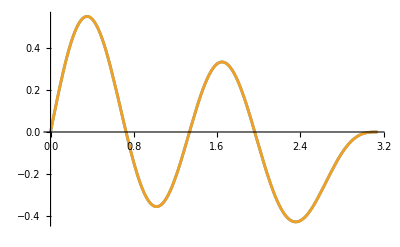

```mathematica
Plot[{Ys2[[1,6]],Ys[[1,6]]},{θ,0,π}]
```

```mathematica
TrigExpand@TrigReduce@Ys2[[1,6]]
TrigExpand@TrigReduce@Ys[[1,6]]
```

-(5 √(77/π) √(1+Cos[θ]))/(128 √(1-Cos[θ]))+(9 √(77/π) Cos[θ] √(1+Cos[θ]))/(128 √(1-Cos[θ]))-(√(77/π) Cos[θ]^2 √(1+Cos[θ]))/(32 √(1-Cos[θ]))-(3 √(77/π) Cos[θ]^3 √(1+Cos[θ]))/(256 √(1-Cos[θ]))+(9 √(77/π) Cos[θ]^4 √(1+Cos[θ]))/(128 √(1-Cos[θ]))-(15 √(77/π) Cos[θ]^5 √(1+Cos[θ]))/(256 √(1-Cos[θ]))+(√(77/π) √(1+Cos[θ]) Sin[θ]^2)/(32 √(1-Cos[θ]))+(9 √(77/π) Cos[θ] √(1+Cos[θ]) Sin[θ]^2)/(256 √(1-Cos[θ]))-(27 √(77/π) Cos[θ]^2 √(1+Cos[θ]) Sin[θ]^2)/(64 √(1-Cos[θ]))+(75 √(77/π) Cos[θ]^3 √(1+Cos[θ]) Sin[θ]^2)/(128 √(1-Cos[θ]))+(9 √(77/π) √(1+Cos[θ]) Sin[θ]^4)/(128 √(1-Cos[θ]))-(75 √(77/π) Cos[θ] √(1+Cos[θ]) Sin[θ]^4)/(256 √(1-Cos[θ]))

-1/128 √(77/π) Sin[θ]+1/16 √(77/π) Cos[θ] Sin[θ]-9/256 √(77/π) Cos[θ]^2 Sin[θ]+3/16 √(77/π) Cos[θ]^3 Sin[θ]+75/256 √(77/π) Cos[θ]^4 Sin[θ]+3/256 √(77/π) Sin[θ]^3-3/16 √(77/π) Cos[θ] Sin[θ]^3-75/128 √(77/π) Cos[θ]^2 Sin[θ]^3+15/256 √(77/π) Sin[θ]^5

## Jumps

```mathematica
ABDsubs={calD->4*π/(r^2*ut),calA->1/Δ[r]*(EE*(r^2+a^2)-a*LL),calB->LL-a*EE};
W0=m*(Ω*(r^2+a^2)-a)/Δ[r];
Q0=m*(1/Sin[θ]-a*Ω*Sin[θ])/.{θ->π/2};
calC2=calB^2*S0;
calC1=2*calB*(I*calA*(S0p+Q0*S0)+calB*(-I*W0+1/r)*S0);
calC0=2*calA*(I*calB*(2/r-I*W0)+calA*(-Q0+I*a/r))*(S0p+Q0*S0)+(calA^2*Λ+calB^2*(I*D[W0,r]-2*I*W0/r-W0^2))*S0;
V0minus4=Δ[r]*(W0^2+I*D[W0,r])-I*D[Δ[r],r]*W0+6*I*m*Ω*r-Λ;
plussubs={S0->Sp2[π/2],S0p->Sp2'[π/2]};
minussubs={m->-mrepl,S0->Sm2[π/2],S0p->Sm2'[π/2]};
Jump0p=calD*Δ[r]*(calC1-D[Δ[r],r]/Δ[r]*calC2)/.plussubs;
Jump1p=calD*Δ[r]*(calC0-V0minus4/Δ[r]*calC2)/.plussubs;
Jump0m=calD*Δ[r]*((calC1-D[Δ[r],r]/Δ[r]*calC2)/.minussubs)/.{mrepl->m};
Jump1m=calD*Δ[r]*((calC0-V0minus4/Δ[r]*calC2)/.minussubs)/.{mrepl->m};
```

```mathematica
Jump0p
```

calD Δ[r] (2 calB (calB Sp2[π/2] (1/r-(ⅈ m (-a+(a^2+r^2) Ω))/Δ[r])+ⅈ calA (m (1-a Ω) Sp2[π/2]+Sp2'[π/2]))-(calB^2 Sp2[π/2] Δ'[r])/Δ[r])

```mathematica
mysubs={LL->r0*v*(1-2*a*v^3+a^2*v^4)/Sqrt[1-3*v^2+2*a*v^3],EE->(1-2*v^2+a*v^3)/Sqrt[1-3*v^2+2*a*v^3],Ω->v^3/(1+a*v^3)}/.{v->1/Sqrt[r0]}/.awsubs;
utsubs={ut->-EE*gup[[1,1]]+LL*gup[[1,4]]}/.ΔKr0subs/.{θ->π/2,r->r0}/.mysubs/.{a->a0};
orbitsubs=Join[mysubs,utsubs];
```

ReplaceAll::reps: {awsubs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ΔKr0subs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{LL→((1+Power[«2»] Power[«2»]-2 a Power[«2»]) √r0)/(√(1+Times[«3»]+Times[«2»])),EE→(1+a Power[«2»]-2 Power[«2»])/(√(1+Times[«3»]+Times[«2»])),Ω→1/((1+Times[«2»]) r0^(3/2))}/.awsubs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

```mathematica
Solve[rstar==r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2]),r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[rstar==r+((rm+rp) (-rm Log[(r-rm)/2]+rp Log[(r-rp)/2]))/(-rm+rp),r]

```mathematica
FullSimplify[Solve[rstar==r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]),r],rp>rm>0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→rp+(rp (rm+rp) ProductLog[(2 (ⅇ^(((rm-rp) (rp-rstar))/(rm rp)))^(rm/(rm+rp)) (-rm+rp))/(rp (rm+rp))])/(-rm+rp)}}

Plot::precw: The precision of the argument function (-(1.8-rstar+1.25 (1.8 Log[1/2 Plus[«2»]]-0.2 Log[1/2 Plus[«2»]])+2.25 ProductLog[0.888889 (ⅇ^Times[«2»])^0.1])/((0.+2.25 ProductLog[0.888889 Power[«2»]^0.1]) (1+1.25 (1.8/Plus[«2»]-0.2/Plus[«2»])))) is less than WorkingPrecision (1000.).

Plot::precw: The precision of the argument function ({1/2 (1.6+2.25 ProductLog[0.888889 Power[«2»]])-0,1/2 (0.+2.25 ProductLog[0.888889 Power[«2»]])-0,«7»,0.888889 Im[(ⅇ^(-4.44444 Plus[«2»]))^0.1]-0,Im[ⅇ^(-4.44444 (1.8-rstar))]-0}) is less than WorkingPrecision (1000.).

Plot::precw: The precision of the argument function ({True,True,True,True,True,True,True,1/2 (1.6+2.25 Re[ProductLog[Times[«2»]]])≤0,1/2 (0.+2.25 Re[ProductLog[Times[«2»]]])≤0,0.888889 Re[(ⅇ^(-4.44444 Plus[«2»]))^0.1]≤-1/ⅇ,Re[ⅇ^(-4.44444 (1.8-rstar))]≤0}) is less than WorkingPrecision (1000.).

General::stop: Further output of Plot::precw will be suppressed during this calculation.

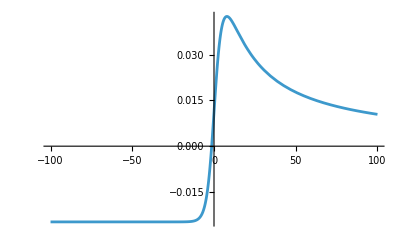

```mathematica
With[{a=0.6},
With[
{rp=1+√(1-a^2),rm=1-√(1-a^2)},
Plot[
Evaluate@{

(-(-rstar+r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2]))/D[-rstar+r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2]),r])/(r-rp)/.{r->rp+(rp (rm+rp) ProductLog[(2 (ⅇ^(((rm-rp) (rp-rstar))/(rm rp)))^(rm/(rm+rp)) (-rm+rp))/(rp (rm+rp))])/(-rm+rp)}
},
{rstar,-100,100},
WorkingPrecision->1000
]
]
]
```

```mathematica
eq0=αup*Rup[r0]-αin*Rin[r0]==Jump0m;
eq1=αup*Rup'[r0]-αin*Rin'[r0]==Jump1m;
```

```mathematica
Solve[{eq0,eq1},{αup,αin}]
```

{{αup→-((-calD Δ[r] Rin'[r0] (2 calB (calB Sm2[π/2] (1/r+(ⅈ m (-a+(a^2+r^2) Ω))/Δ[r])+ⅈ calA (-m (1-a Ω) Sm2[π/2]+Sm2'[π/2]))-(calB^2 Sm2[π/2] Δ'[r])/Δ[r])+calD Rin[r0] Δ[r] (2 calA (calA ((ⅈ a)/r+m (1-a Ω))+ⅈ calB (2/r+(ⅈ m (-a+(a^2+r^2) Ω))/Δ[r])) (-m (1-a Ω) Sm2[π/2]+Sm2'[π/2])-1/Δ[r]calB^2 Sm2[π/2] (-Λ-6 ⅈ m r Ω+(ⅈ m (-a+(a^2+r^2) Ω) Δ'[r])/Δ[r]+Δ[r] ((m^2 (-a+(a^2+r^2) Ω)^2)/Δ[r]^2+ⅈ (-(2 m r Ω)/Δ[r]+(m (-a+(a^2+r^2) Ω) Δ'[r])/Δ[r]^2)))+Sm2[π/2] (calA^2 Λ+calB^2 (-(m^2 (-a+(a^2+r^2) Ω)^2)/Δ[r]^2+(2 ⅈ m (-a+(a^2+r^2) Ω))/(r Δ[r])+ⅈ (-(2 m r Ω)/Δ[r]+(m (-a+(a^2+r^2) Ω) Δ'[r])/Δ[r]^2)))))/(Rup[r0] Rin'[r0]-Rin[r0] Rup'[r0])),αin→(calD (2 a^2 calB^2 m^2 r Rup[r0] Sm2[π/2]-4 a^3 calB^2 m^2 r Ω Rup[r0] Sm2[π/2]-4 a calB^2 m^2 r^3 Ω Rup[r0] Sm2[π/2]+2 a^4 calB^2 m^2 r Ω^2 Rup[r0] Sm2[π/2]+4 a^2 calB^2 m^2 r^3 Ω^2 Rup[r0] Sm2[π/2]+2 calB^2 m^2 r^5 Ω^2 Rup[r0] Sm2[π/2]+2 ⅈ a calB^2 m Rup[r0] Sm2[π/2] Δ[r]+2 a calA calB m^2 r Rup[r0] Sm2[π/2] Δ[r]-calB^2 r Λ Rup[r0] Sm2[π/2] Δ[r]-2 ⅈ a^2 calB^2 m Ω Rup[r0] Sm2[π/2] Δ[r]-4 a^2 calA calB m^2 r Ω Rup[r0] Sm2[π/2] Δ[r]-8 ⅈ calB^2 m r^2 Ω Rup[r0] Sm2[π/2] Δ[r]-2 calA calB m^2 r^3 Ω Rup[r0] Sm2[π/2] Δ[r]+2 a^3 calA calB m^2 r Ω^2 Rup[r0] Sm2[π/2] Δ[r]+2 a calA calB m^2 r^3 Ω^2 Rup[r0] Sm2[π/2] Δ[r]+2 ⅈ a calA^2 m Rup[r0] Sm2[π/2] Δ[r]^2+4 ⅈ calA calB m Rup[r0] Sm2[π/2] Δ[r]^2+2 calA^2 m^2 r Rup[r0] Sm2[π/2] Δ[r]^2-calA^2 r Λ Rup[r0] Sm2[π/2] Δ[r]^2-2 ⅈ a^2 calA^2 m Ω Rup[r0] Sm2[π/2] Δ[r]^2-4 ⅈ a calA calB m Ω Rup[r0] Sm2[π/2] Δ[r]^2-4 a calA^2 m^2 r Ω Rup[r0] Sm2[π/2] Δ[r]^2+2 a^2 calA^2 m^2 r Ω^2 Rup[r0] Sm2[π/2] Δ[r]^2-2 ⅈ a calB^2 m r Sm2[π/2] Δ[r] Rup'[r0]+2 ⅈ a^2 calB^2 m r Ω Sm2[π/2] Δ[r] Rup'[r0]+2 ⅈ calB^2 m r^3 Ω Sm2[π/2] Δ[r] Rup'[r0]+2 calB^2 Sm2[π/2] Δ[r]^2 Rup'[r0]-2 ⅈ calA calB m r Sm2[π/2] Δ[r]^2 Rup'[r0]+2 ⅈ a calA calB m r Ω Sm2[π/2] Δ[r]^2 Rup'[r0]-2 a calA calB m r Rup[r0] Δ[r] Sm2'[π/2]+2 a^2 calA calB m r Ω Rup[r0] Δ[r] Sm2'[π/2]+2 calA calB m r^3 Ω Rup[r0] Δ[r] Sm2'[π/2]-2 ⅈ a calA^2 Rup[r0] Δ[r]^2 Sm2'[π/2]-4 ⅈ calA calB Rup[r0] Δ[r]^2 Sm2'[π/2]-2 calA^2 m r Rup[r0] Δ[r]^2 Sm2'[π/2]+2 a calA^2 m r Ω Rup[r0] Δ[r]^2 Sm2'[π/2]+2 ⅈ calA calB r Δ[r]^2 Rup'[r0] Sm2'[π/2]-ⅈ a calB^2 m r Rup[r0] Sm2[π/2] Δ'[r]+ⅈ a^2 calB^2 m r Ω Rup[r0] Sm2[π/2] Δ'[r]+ⅈ calB^2 m r^3 Ω Rup[r0] Sm2[π/2] Δ'[r]-calB^2 r Sm2[π/2] Δ[r] Rup'[r0] Δ'[r]))/(r Δ[r] (Rup[r0] Rin'[r0]-Rin[r0] Rup'[r0]))}}

```mathematica
Jump0m
```

calD Δ[r] (2 calB (calB Sm2[π/2] (1/r+(ⅈ m (-a+(a^2+r^2) Ω))/Δ[r])+ⅈ calA (-m (1-a Ω) Sm2[π/2]+Sm2'[π/2]))-(calB^2 Sm2[π/2] Δ'[r])/Δ[r])

```mathematica
Calcαup[OD_OrbitalData,{s_,l_,m_},{Rin_,Rinp_,W_},{}]
```

## Calcs2components

```mathematica
λhat[lmax_,m_]:=λhat[lmax,m]=DiagonalMatrix[Table[If[ll<Abs[m],0,Sqrt[ll*(ll+1)]],{ll,0,lmax}]];
λhat2[lmax_,m_]:=λhat2[lmax,m]=DiagonalMatrix[Table[If[ll<Max[Abs[m],1],0,Sqrt[(ll-1)*(ll+2)]],{ll,0,lmax}]];
Λhat[lmax_,m_]:=Λhat[lmax,m]=λhat[lmax,m]λ2hat[lmax,m]
signmat[lmax_,m_]:=signmat[lmax,m]=DiagonalMatrix[Table[If[ll<Abs[m],0,(-1)^(ll+m)],{ll,0,lmax}]];
idmat[lmax_,m_]:=idmat[lmax,m]=DiagonalMatrix[Table[If[ll<Abs[m],0,1],{ll,0,lmax}]];
```

```mathematica
(*  Calcs2components  *)
t0=Bmatp2 . (Λhat-2*aω0*λ2hat . SinMixMatrix[1,0,lmax,mm]+aω0^2*SinMixMatrix[2,0,lmax,mm]);
t1=signmat . Bmatm2 . (Λhat-2*aω0*λ2hat . SinMixMatrix[-1,0,lmax,mm]+aω0^2*SinMixMatrix[-2,0,lmax,mm]);
Ss2lplp=(t0+t1)/.awsubs;
Ss2lmlm=signmat . Ss2lplp/.awsubs; 
Ss2mpmp=Bmatp2/.awsubs;
Ss2mmmm=signmat . Bmatm2/.awsubs;
SSplus=(Bmatp2 . (Λhat-2*a*ω*λ2hat . SinMixMatrix[1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[2,0,lmax,mm]))/.awsubs;
SSminus=(Bmatm2 . (Λhat-2*a*ω*λ2hat . SinMixMatrix[-1,0,lmax,mm]+a^2*ω^2*SinMixMatrix[-2,0,lmax,mm]))/.awsubs;
```

```mathematica
(* Attach an a-prefix before they have been evaluated numerically. *)
aPp2vec={Pp2[r]};
aPm2vec={Pm2[r]};
aDdagPp2vec=Map[Ddag,aPp2vec]/.ΔKsimp;
aDdagDdagPp2vec=Map[Ddag,aDdagPp2vec]/.ΔKsimp;
aDdagDdagDdagPp2vec=Map[Ddag,aDdagDdagPp2vec]/.ΔKsimp;
aDPm2vec=Map[Dop,aPm2vec]/.ΔKsimp;
aDDPm2vec=Map[Dop,aDPm2vec]/.ΔKsimp;
aDDDPm2vec=Map[Dop,aDDPm2vec]/.ΔKsimp;
aDopDdagDdagPp2vec=Map[Dop,aDdagDdagPp2vec]/.ΔKsimp;
aDdagDDPm2vec=Map[Ddag,aDDPm2vec]/.ΔKsimp;
```

```mathematica
alplmterm1A=Map[Dop,Δ[r]*Map[Ddag,aDDPm2vec]]+Map[Ddag,Δ[r]*Map[Dop,aDDPm2vec]];
alplmterm1B=Map[D[#,r]&,aDDPm2vec];
alplmterm2A=Map[Dop,Δ[r]*Map[Ddag,aDdagDdagPp2vec]]+Map[Ddag,Δ[r]*Map[Dop,aDdagDdagPp2vec]];
alplmterm2B=Map[D[#,r]&,aDdagDdagPp2vec];
```

```mathematica
Clear[cosmix,sinmix];
sinp1=SinMixMatrix[0,1,lmax,mm];
sinm1=SinMixMatrix[0,-1,lmax,mm];
sinmix1m1a=SinMixMatrix[-1,1,lmax,mm];
sinmix1m1b=SinMixMatrix[1,-1,lmax,mm];
ρmat1=r*idmat+I*a*CosMixMatrix[1,1,lmax,mm];  (* These should be used for the first two components: l+m+ and l+m- *)
ρcmat1=r*idmat-I*a*CosMixMatrix[-1,1,lmax,mm];
ρcmat2=r*idmat-I*a*CosMixMatrix[1,1,lmax,mm]; (* These should be used for the second components: l-m+ and l-m- *)
ρmat2=r*idmat+I*a*CosMixMatrix[-1,1,lmax,mm];
cosmix01=CosMixMatrix[0,1,lmax,mm];
cosmix02=CosMixMatrix[0,2,lmax,mm];
ρcmat3=r*idmat-I*a*cosmix01;  (* These should be used for l+l- *) 
ρmat3=r*idmat+I*a*cosmix01;
Σmat=r^2*idmat+a^2*cosmix02;
sinp10=SinMixMatrix[1,0,lmax,mm];
sinm10=SinMixMatrix[-1,0,lmax,mm];
MMp2=Bmatp2 . (λ2hat-a*ω*SinMixMatrix[2,1,lmax,mm]);
MMm2=Bmatm2 . (λ2hat-a*ω*SinMixMatrix[-2,-1,lmax,mm]);
```

#### Pvecs

```mathematica
bla=Collect[First/@{
aPp2vec,
aPm2vec,
aDdagPp2vec,
aDdagDdagPp2vec,
aDdagDdagDdagPp2vec,
aDPm2vec,
aDDPm2vec,
aDDDPm2vec,
aDopDdagDdagPp2vec,
aDdagDDPm2vec
}/.ΔKsimp/.ΔKsubs/.M->1,{f_[r]},Factor@*Together]/.{Derivative[n_.][P_][r]:> ToExpression[ToString[P]<>ToString[n]],Pm2[r]->Pm2,Pp2[r]->Pp2};
```

```mathematica
Numerator
```

```mathematica
bla[[3]]
```

Pp21+(ⅈ Pp2 (-a m+(a^2+r^2) ω))/(a^2-2 r+r^2)

```mathematica
aDdagPp2[a_,m_,ω_,r_]:=Function[{Pp2,Pp21,Pp22,Pp23,Pp24},Evaluate[
Pp21+(ⅈ Pp2 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)
]
]
```

```mathematica
bla[[4]]
```

Pp22+(2 ⅈ Pp21 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(Pp2 (2 ⅈ a m+a^2 m^2-2 ⅈ a m r-2 ⅈ a^2 ω-2 a^3 m ω+2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)

```mathematica
aDdagDdagPp2[a_,m_,ω_,r_]:=Function[{Pp2,Pp21,Pp22,Pp23,Pp24},Evaluate[
Pp22+(2 ⅈ Pp21 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(Pp2 (2 ⅈ a m+a^2 m^2-2 ⅈ a m r-2 ⅈ a^2 ω-2 a^3 m ω+2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)
]
]
```

```mathematica
bla[[5]]
```

Pp23+(3 ⅈ Pp22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(3 Pp21 (2 ⅈ a m+a^2 m^2-2 ⅈ a m r-2 ⅈ a^2 ω-2 a^3 m ω+2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pp2 (-8 ⅈ a m+2 ⅈ a^3 m-6 a^2 m^2+ⅈ a^3 m^3+12 ⅈ a m r+6 a^2 m^2 r-6 ⅈ a m r^2+8 ⅈ a^2 ω+12 a^3 m ω-3 ⅈ a^4 m^2 ω-12 ⅈ a^2 r ω-6 a^3 m r ω-3 ⅈ a^2 m^2 r^2 ω+4 ⅈ r^3 ω-6 a m r^3 ω-6 a^4 ω^2+3 ⅈ a^5 m ω^2+6 ⅈ a^3 m r^2 ω^2+6 r^4 ω^2+3 ⅈ a m r^4 ω^2-ⅈ a^6 ω^3-3 ⅈ a^4 r^2 ω^3-3 ⅈ a^2 r^4 ω^3-ⅈ r^6 ω^3)

```mathematica
aDdagDdagDdagPp2[a_,m_,ω_,r_]:=Function[{Pp2,Pp21,Pp22,Pp23,Pp24},Evaluate[
Pp23+(3 ⅈ Pp22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(3 Pp21 (2 ⅈ a m+a^2 m^2-2 ⅈ a m r-2 ⅈ a^2 ω-2 a^3 m ω+2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pp2 (-8 ⅈ a m+2 ⅈ a^3 m-6 a^2 m^2+ⅈ a^3 m^3+12 ⅈ a m r+6 a^2 m^2 r-6 ⅈ a m r^2+8 ⅈ a^2 ω+12 a^3 m ω-3 ⅈ a^4 m^2 ω-12 ⅈ a^2 r ω-6 a^3 m r ω-3 ⅈ a^2 m^2 r^2 ω+4 ⅈ r^3 ω-6 a m r^3 ω-6 a^4 ω^2+3 ⅈ a^5 m ω^2+6 ⅈ a^3 m r^2 ω^2+6 r^4 ω^2+3 ⅈ a m r^4 ω^2-ⅈ a^6 ω^3-3 ⅈ a^4 r^2 ω^3-3 ⅈ a^2 r^4 ω^3-ⅈ r^6 ω^3)
]
]
```

SetDelayed::write: Tag List in «1» is Protected.

$Failed

```mathematica
bla[[7]]
```

Pm22-(2 ⅈ Pm21 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(Pm2 (-2 ⅈ a m+a^2 m^2+2 ⅈ a m r+2 ⅈ a^2 ω-2 a^3 m ω-2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)

```mathematica
aDDPm2[a_,m_,ω_,r_]:=Function[{Pm2,Pm21,Pm22,Pm23,Pm24},Evaluate[
Pm22-(2 ⅈ Pm21 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(Pm2 (-2 ⅈ a m+a^2 m^2+2 ⅈ a m r+2 ⅈ a^2 ω-2 a^3 m ω-2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)
]
]
```

```mathematica
bla[[8]]
```

Pm23-(3 ⅈ Pm22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(3 Pm21 (-2 ⅈ a m+a^2 m^2+2 ⅈ a m r+2 ⅈ a^2 ω-2 a^3 m ω-2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pm2 (8 ⅈ a m-2 ⅈ a^3 m-6 a^2 m^2-ⅈ a^3 m^3-12 ⅈ a m r+6 a^2 m^2 r+6 ⅈ a m r^2-8 ⅈ a^2 ω+12 a^3 m ω+3 ⅈ a^4 m^2 ω+12 ⅈ a^2 r ω-6 a^3 m r ω+3 ⅈ a^2 m^2 r^2 ω-4 ⅈ r^3 ω-6 a m r^3 ω-6 a^4 ω^2-3 ⅈ a^5 m ω^2-6 ⅈ a^3 m r^2 ω^2+6 r^4 ω^2-3 ⅈ a m r^4 ω^2+ⅈ a^6 ω^3+3 ⅈ a^4 r^2 ω^3+3 ⅈ a^2 r^4 ω^3+ⅈ r^6 ω^3)

```mathematica
aDDDPm2[a_,m_,ω_,r_]:=Function[{Pm2,Pm21,Pm22,Pm23,Pm24},Evaluate[
Pm23-(3 ⅈ Pm22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-(3 Pm21 (-2 ⅈ a m+a^2 m^2+2 ⅈ a m r+2 ⅈ a^2 ω-2 a^3 m ω-2 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pm2 (8 ⅈ a m-2 ⅈ a^3 m-6 a^2 m^2-ⅈ a^3 m^3-12 ⅈ a m r+6 a^2 m^2 r+6 ⅈ a m r^2-8 ⅈ a^2 ω+12 a^3 m ω+3 ⅈ a^4 m^2 ω+12 ⅈ a^2 r ω-6 a^3 m r ω+3 ⅈ a^2 m^2 r^2 ω-4 ⅈ r^3 ω-6 a m r^3 ω-6 a^4 ω^2-3 ⅈ a^5 m ω^2-6 ⅈ a^3 m r^2 ω^2+6 r^4 ω^2-3 ⅈ a m r^4 ω^2+ⅈ a^6 ω^3+3 ⅈ a^4 r^2 ω^3+3 ⅈ a^2 r^4 ω^3+ⅈ r^6 ω^3)
]
]
```

```mathematica
bla[[9]]
```

Pp23+(ⅈ Pp22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)+(Pp21 (-6 ⅈ a m+a^2 m^2+6 ⅈ a m r+6 ⅈ a^2 ω-2 a^3 m ω-6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pp2 (-8 ⅈ a m+2 ⅈ a^3 m-2 a^2 m^2-ⅈ a^3 m^3+12 ⅈ a m r+2 a^2 m^2 r-6 ⅈ a m r^2+8 ⅈ a^2 ω+4 a^3 m ω+3 ⅈ a^4 m^2 ω-12 ⅈ a^2 r ω-2 a^3 m r ω+3 ⅈ a^2 m^2 r^2 ω+4 ⅈ r^3 ω-2 a m r^3 ω-2 a^4 ω^2-3 ⅈ a^5 m ω^2-6 ⅈ a^3 m r^2 ω^2+2 r^4 ω^2-3 ⅈ a m r^4 ω^2+ⅈ a^6 ω^3+3 ⅈ a^4 r^2 ω^3+3 ⅈ a^2 r^4 ω^3+ⅈ r^6 ω^3)

```mathematica
aDopDdagDdagPp2[a_,m_,ω_,r_]:=Function[{Pp2,Pp21,Pp22,Pp23,Pp24},Evaluate[
Pp23+(ⅈ Pp22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)+(Pp21 (-6 ⅈ a m+a^2 m^2+6 ⅈ a m r+6 ⅈ a^2 ω-2 a^3 m ω-6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pp2 (-8 ⅈ a m+2 ⅈ a^3 m-2 a^2 m^2-ⅈ a^3 m^3+12 ⅈ a m r+2 a^2 m^2 r-6 ⅈ a m r^2+8 ⅈ a^2 ω+4 a^3 m ω+3 ⅈ a^4 m^2 ω-12 ⅈ a^2 r ω-2 a^3 m r ω+3 ⅈ a^2 m^2 r^2 ω+4 ⅈ r^3 ω-2 a m r^3 ω-2 a^4 ω^2-3 ⅈ a^5 m ω^2-6 ⅈ a^3 m r^2 ω^2+2 r^4 ω^2-3 ⅈ a m r^4 ω^2+ⅈ a^6 ω^3+3 ⅈ a^4 r^2 ω^3+3 ⅈ a^2 r^4 ω^3+ⅈ r^6 ω^3)
]
]
```

```mathematica
bla[[10]]
```

Pm23-(ⅈ Pm22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)+(Pm21 (6 ⅈ a m+a^2 m^2-6 ⅈ a m r-6 ⅈ a^2 ω-2 a^3 m ω+6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pm2 (8 ⅈ a m-2 ⅈ a^3 m-2 a^2 m^2+ⅈ a^3 m^3-12 ⅈ a m r+2 a^2 m^2 r+6 ⅈ a m r^2-8 ⅈ a^2 ω+4 a^3 m ω-3 ⅈ a^4 m^2 ω+12 ⅈ a^2 r ω-2 a^3 m r ω-3 ⅈ a^2 m^2 r^2 ω-4 ⅈ r^3 ω-2 a m r^3 ω-2 a^4 ω^2+3 ⅈ a^5 m ω^2+6 ⅈ a^3 m r^2 ω^2+2 r^4 ω^2+3 ⅈ a m r^4 ω^2-ⅈ a^6 ω^3-3 ⅈ a^4 r^2 ω^3-3 ⅈ a^2 r^4 ω^3-ⅈ r^6 ω^3)

```mathematica
aDdagDDPm2[a_,m_,ω_,r_]:=Function[{Pm2,Pm21,Pm22,Pm23,Pm24},Evaluate[
Pm23-(ⅈ Pm22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)+(Pm21 (6 ⅈ a m+a^2 m^2-6 ⅈ a m r-6 ⅈ a^2 ω-2 a^3 m ω+6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)+1/((a^2-2 r+r^2)^3)Pm2 (8 ⅈ a m-2 ⅈ a^3 m-2 a^2 m^2+ⅈ a^3 m^3-12 ⅈ a m r+2 a^2 m^2 r+6 ⅈ a m r^2-8 ⅈ a^2 ω+4 a^3 m ω-3 ⅈ a^4 m^2 ω+12 ⅈ a^2 r ω-2 a^3 m r ω-3 ⅈ a^2 m^2 r^2 ω-4 ⅈ r^3 ω-2 a m r^3 ω-2 a^4 ω^2+3 ⅈ a^5 m ω^2+6 ⅈ a^3 m r^2 ω^2+2 r^4 ω^2+3 ⅈ a m r^4 ω^2-ⅈ a^6 ω^3-3 ⅈ a^4 r^2 ω^3-3 ⅈ a^2 r^4 ω^3-ⅈ r^6 ω^3)
]
]
```

```mathematica
Collect[First/@{alplmterm1A,alplmterm1B,alplmterm2A,alplmterm2B}/.ΔKsimp/.ΔKsubs/.M->1,f_[r],Factor@*Together]/.{Derivative[n_.][P_][r]:> ToExpression[ToString[P]<>ToString[n]],Pm2[r]->Pm2,Pp2[r]->Pp2}
```

{2 Pm24 (a^2-2 r+r^2)+4 Pm23 (-1+ⅈ a m+r-ⅈ a^2 ω-ⅈ r^2 ω)-(4 ⅈ Pm22 (-3 a m+3 a m r+3 a^2 ω+2 a^2 r ω-7 r^2 ω+2 r^3 ω))/(a^2-2 r+r^2)+1/((a^2-2 r+r^2)^2)4 Pm21 (10 ⅈ a m-4 ⅈ a^3 m-3 a^2 m^2+ⅈ a^3 m^3-12 ⅈ a m r+3 a^2 m^2 r+6 ⅈ a m r^2-10 ⅈ a^2 ω+6 a^3 m ω-3 ⅈ a^4 m^2 ω+18 ⅈ a^2 r ω-2 a^3 m r ω-6 ⅈ r^2 ω-2 a m r^2 ω-3 ⅈ a^2 m^2 r^2 ω-2 ⅈ r^3 ω-2 a m r^3 ω-3 a^4 ω^2+3 ⅈ a^5 m ω^2-a^4 r ω^2+2 a^2 r^2 ω^2+6 ⅈ a^3 m r^2 ω^2-2 a^2 r^3 ω^2+5 r^4 ω^2+3 ⅈ a m r^4 ω^2-r^5 ω^2-ⅈ a^6 ω^3-3 ⅈ a^4 r^2 ω^3-3 ⅈ a^2 r^4 ω^3-ⅈ r^6 ω^3)-1/((a^2-2 r+r^2)^3)2 Pm2 (-32 ⅈ a m+20 ⅈ a^3 m+16 a^2 m^2-4 a^4 m^2-2 ⅈ a^3 m^3+a^4 m^4+56 ⅈ a m r-20 ⅈ a^3 m r-24 a^2 m^2 r+2 ⅈ a^3 m^3 r-36 ⅈ a m r^2+12 a^2 m^2 r^2+12 ⅈ a m r^3+32 ⅈ a^2 ω-12 ⅈ a^4 ω-32 a^3 m ω+4 a^5 m ω+6 ⅈ a^4 m^2 ω-4 a^5 m^3 ω-56 ⅈ a^2 r ω+40 a^3 m r ω-4 ⅈ a^4 m^2 r ω+48 ⅈ a^2 r^2 ω+2 ⅈ a^2 m^2 r^2 ω-4 a^3 m^3 r^2 ω-8 ⅈ r^3 ω-8 a m r^3 ω-4 ⅈ a^2 m^2 r^3 ω-4 ⅈ r^4 ω-4 a m r^4 ω+16 a^4 ω^2-6 ⅈ a^5 m ω^2+6 a^6 m^2 ω^2-16 a^4 r ω^2+2 ⅈ a^5 m r ω^2-4 ⅈ a^3 m r^2 ω^2+12 a^4 m^2 r^2 ω^2-16 a^2 r^3 ω^2+4 ⅈ a^3 m r^3 ω^2+16 r^4 ω^2+2 ⅈ a m r^4 ω^2+6 a^2 m^2 r^4 ω^2+2 ⅈ a m r^5 ω^2+2 ⅈ a^6 ω^3-4 a^7 m ω^3+2 ⅈ a^4 r^2 ω^3-12 a^5 m r^2 ω^3-2 ⅈ a^2 r^4 ω^3-12 a^3 m r^4 ω^3-2 ⅈ r^6 ω^3-4 a m r^6 ω^3+a^8 ω^4+4 a^6 r^2 ω^4+6 a^4 r^4 ω^4+4 a^2 r^6 ω^4+r^8 ω^4),Pm23-(2 ⅈ Pm22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-1/((a^2-2 r+r^2)^3)2 Pm2 (-4 ⅈ a m+ⅈ a^3 m+2 a^2 m^2+6 ⅈ a m r-2 a^2 m^2 r-3 ⅈ a m r^2+4 ⅈ a^2 ω-4 a^3 m ω-6 ⅈ a^2 r ω+2 a^3 m r ω+2 ⅈ r^3 ω+2 a m r^3 ω+2 a^4 ω^2-2 r^4 ω^2)-(Pm21 (-6 ⅈ a m+a^2 m^2+6 ⅈ a m r+6 ⅈ a^2 ω-2 a^3 m ω-6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2),2 Pp24 (a^2-2 r+r^2)+4 Pp23 (-1-ⅈ a m+r+ⅈ a^2 ω+ⅈ r^2 ω)+(4 ⅈ Pp22 (-3 a m+3 a m r+3 a^2 ω+2 a^2 r ω-7 r^2 ω+2 r^3 ω))/(a^2-2 r+r^2)+1/((a^2-2 r+r^2)^2)4 Pp21 (-10 ⅈ a m+4 ⅈ a^3 m-3 a^2 m^2-ⅈ a^3 m^3+12 ⅈ a m r+3 a^2 m^2 r-6 ⅈ a m r^2+10 ⅈ a^2 ω+6 a^3 m ω+3 ⅈ a^4 m^2 ω-18 ⅈ a^2 r ω-2 a^3 m r ω+6 ⅈ r^2 ω-2 a m r^2 ω+3 ⅈ a^2 m^2 r^2 ω+2 ⅈ r^3 ω-2 a m r^3 ω-3 a^4 ω^2-3 ⅈ a^5 m ω^2-a^4 r ω^2+2 a^2 r^2 ω^2-6 ⅈ a^3 m r^2 ω^2-2 a^2 r^3 ω^2+5 r^4 ω^2-3 ⅈ a m r^4 ω^2-r^5 ω^2+ⅈ a^6 ω^3+3 ⅈ a^4 r^2 ω^3+3 ⅈ a^2 r^4 ω^3+ⅈ r^6 ω^3)-1/((a^2-2 r+r^2)^3)2 Pp2 (32 ⅈ a m-20 ⅈ a^3 m+16 a^2 m^2-4 a^4 m^2+2 ⅈ a^3 m^3+a^4 m^4-56 ⅈ a m r+20 ⅈ a^3 m r-24 a^2 m^2 r-2 ⅈ a^3 m^3 r+36 ⅈ a m r^2+12 a^2 m^2 r^2-12 ⅈ a m r^3-32 ⅈ a^2 ω+12 ⅈ a^4 ω-32 a^3 m ω+4 a^5 m ω-6 ⅈ a^4 m^2 ω-4 a^5 m^3 ω+56 ⅈ a^2 r ω+40 a^3 m r ω+4 ⅈ a^4 m^2 r ω-48 ⅈ a^2 r^2 ω-2 ⅈ a^2 m^2 r^2 ω-4 a^3 m^3 r^2 ω+8 ⅈ r^3 ω-8 a m r^3 ω+4 ⅈ a^2 m^2 r^3 ω+4 ⅈ r^4 ω-4 a m r^4 ω+16 a^4 ω^2+6 ⅈ a^5 m ω^2+6 a^6 m^2 ω^2-16 a^4 r ω^2-2 ⅈ a^5 m r ω^2+4 ⅈ a^3 m r^2 ω^2+12 a^4 m^2 r^2 ω^2-16 a^2 r^3 ω^2-4 ⅈ a^3 m r^3 ω^2+16 r^4 ω^2-2 ⅈ a m r^4 ω^2+6 a^2 m^2 r^4 ω^2-2 ⅈ a m r^5 ω^2-2 ⅈ a^6 ω^3-4 a^7 m ω^3-2 ⅈ a^4 r^2 ω^3-12 a^5 m r^2 ω^3+2 ⅈ a^2 r^4 ω^3-12 a^3 m r^4 ω^3+2 ⅈ r^6 ω^3-4 a m r^6 ω^3+a^8 ω^4+4 a^6 r^2 ω^4+6 a^4 r^4 ω^4+4 a^2 r^6 ω^4+r^8 ω^4),Pp23+(2 ⅈ Pp22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-1/((a^2-2 r+r^2)^3)2 Pp2 (4 ⅈ a m-ⅈ a^3 m+2 a^2 m^2-6 ⅈ a m r-2 a^2 m^2 r+3 ⅈ a m r^2-4 ⅈ a^2 ω-4 a^3 m ω+6 ⅈ a^2 r ω+2 a^3 m r ω-2 ⅈ r^3 ω+2 a m r^3 ω+2 a^4 ω^2-2 r^4 ω^2)-(Pp21 (6 ⅈ a m+a^2 m^2-6 ⅈ a m r-6 ⅈ a^2 ω-2 a^3 m ω+6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)}

```mathematica
alplmterm1A[a_,m_,ω_,r_]:=Function[{Pm2,Pm21,Pm22,Pm23,Pm24},Evaluate[
2 Pm24 (a^2-2 r+r^2)+4 Pm23 (-1+ⅈ a m+r-ⅈ a^2 ω-ⅈ r^2 ω)-(4 ⅈ Pm22 (-3 a m+3 a m r+3 a^2 ω+2 a^2 r ω-7 r^2 ω+2 r^3 ω))/(a^2-2 r+r^2)+1/((a^2-2 r+r^2)^2)4 Pm21 (10 ⅈ a m-4 ⅈ a^3 m-3 a^2 m^2+ⅈ a^3 m^3-12 ⅈ a m r+3 a^2 m^2 r+6 ⅈ a m r^2-10 ⅈ a^2 ω+6 a^3 m ω-3 ⅈ a^4 m^2 ω+18 ⅈ a^2 r ω-2 a^3 m r ω-6 ⅈ r^2 ω-2 a m r^2 ω-3 ⅈ a^2 m^2 r^2 ω-2 ⅈ r^3 ω-2 a m r^3 ω-3 a^4 ω^2+3 ⅈ a^5 m ω^2-a^4 r ω^2+2 a^2 r^2 ω^2+6 ⅈ a^3 m r^2 ω^2-2 a^2 r^3 ω^2+5 r^4 ω^2+3 ⅈ a m r^4 ω^2-r^5 ω^2-ⅈ a^6 ω^3-3 ⅈ a^4 r^2 ω^3-3 ⅈ a^2 r^4 ω^3-ⅈ r^6 ω^3)-1/((a^2-2 r+r^2)^3)2 Pm2 (-32 ⅈ a m+20 ⅈ a^3 m+16 a^2 m^2-4 a^4 m^2-2 ⅈ a^3 m^3+a^4 m^4+56 ⅈ a m r-20 ⅈ a^3 m r-24 a^2 m^2 r+2 ⅈ a^3 m^3 r-36 ⅈ a m r^2+12 a^2 m^2 r^2+12 ⅈ a m r^3+32 ⅈ a^2 ω-12 ⅈ a^4 ω-32 a^3 m ω+4 a^5 m ω+6 ⅈ a^4 m^2 ω-4 a^5 m^3 ω-56 ⅈ a^2 r ω+40 a^3 m r ω-4 ⅈ a^4 m^2 r ω+48 ⅈ a^2 r^2 ω+2 ⅈ a^2 m^2 r^2 ω-4 a^3 m^3 r^2 ω-8 ⅈ r^3 ω-8 a m r^3 ω-4 ⅈ a^2 m^2 r^3 ω-4 ⅈ r^4 ω-4 a m r^4 ω+16 a^4 ω^2-6 ⅈ a^5 m ω^2+6 a^6 m^2 ω^2-16 a^4 r ω^2+2 ⅈ a^5 m r ω^2-4 ⅈ a^3 m r^2 ω^2+12 a^4 m^2 r^2 ω^2-16 a^2 r^3 ω^2+4 ⅈ a^3 m r^3 ω^2+16 r^4 ω^2+2 ⅈ a m r^4 ω^2+6 a^2 m^2 r^4 ω^2+2 ⅈ a m r^5 ω^2+2 ⅈ a^6 ω^3-4 a^7 m ω^3+2 ⅈ a^4 r^2 ω^3-12 a^5 m r^2 ω^3-2 ⅈ a^2 r^4 ω^3-12 a^3 m r^4 ω^3-2 ⅈ r^6 ω^3-4 a m r^6 ω^3+a^8 ω^4+4 a^6 r^2 ω^4+6 a^4 r^4 ω^4+4 a^2 r^6 ω^4+r^8 ω^4)
]
]
```

```mathematica
alplmterm1B[a_,m_,ω_,r_]:=Function[{Pm2,Pm21,Pm22,Pm23,Pm24},Evaluate[
Pm23-(2 ⅈ Pm22 (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2)-1/((a^2-2 r+r^2)^3)2 Pm2 (-4 ⅈ a m+ⅈ a^3 m+2 a^2 m^2+6 ⅈ a m r-2 a^2 m^2 r-3 ⅈ a m r^2+4 ⅈ a^2 ω-4 a^3 m ω-6 ⅈ a^2 r ω+2 a^3 m r ω+2 ⅈ r^3 ω+2 a m r^3 ω+2 a^4 ω^2-2 r^4 ω^2)-(Pm21 (-6 ⅈ a m+a^2 m^2+6 ⅈ a m r+6 ⅈ a^2 ω-2 a^3 m ω-6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2))/((a^2-2 r+r^2)^2)
]
]
```

```mathematica
alplmterm2A[a_,m_,ω_,r_]:=Function[{Pp2,Pp21,Pp22,Pp23,Pp24},Evaluate[
2 Pp24 (a^2-2 r+r^2)+4 Pp23 (-1-ⅈ a m+r+ⅈ a^2 ω+ⅈ r^2 ω)+(4 ⅈ Pp22 (-3 a m+3 a m r+3 a^2 ω+2 a^2 r ω-7 r^2 ω+2 r^3 ω))/(a^2-2 r+r^2)+1/((a^2-2 r+r^2)^2)4 Pp21 (-10 ⅈ a m+4 ⅈ a^3 m-3 a^2 m^2-ⅈ a^3 m^3+12 ⅈ a m r+3 a^2 m^2 r-6 ⅈ a m r^2+10 ⅈ a^2 ω+6 a^3 m ω+3 ⅈ a^4 m^2 ω-18 ⅈ a^2 r ω-2 a^3 m r ω+6 ⅈ r^2 ω-2 a m r^2 ω+3 ⅈ a^2 m^2 r^2 ω+2 ⅈ r^3 ω-2 a m r^3 ω-3 a^4 ω^2-3 ⅈ a^5 m ω^2-a^4 r ω^2+2 a^2 r^2 ω^2-6 ⅈ a^3 m r^2 ω^2-2 a^2 r^3 ω^2+5 r^4 ω^2-3 ⅈ a m r^4 ω^2-r^5 ω^2+ⅈ a^6 ω^3+3 ⅈ a^4 r^2 ω^3+3 ⅈ a^2 r^4 ω^3+ⅈ r^6 ω^3)-1/((a^2-2 r+r^2)^3)2 Pp2 (32 ⅈ a m-20 ⅈ a^3 m+16 a^2 m^2-4 a^4 m^2+2 ⅈ a^3 m^3+a^4 m^4-56 ⅈ a m r+20 ⅈ a^3 m r-24 a^2 m^2 r-2 ⅈ a^3 m^3 r+36 ⅈ a m r^2+12 a^2 m^2 r^2-12 ⅈ a m r^3-32 ⅈ a^2 ω+12 ⅈ a^4 ω-32 a^3 m ω+4 a^5 m ω-6 ⅈ a^4 m^2 ω-4 a^5 m^3 ω+56 ⅈ a^2 r ω+40 a^3 m r ω+4 ⅈ a^4 m^2 r ω-48 ⅈ a^2 r^2 ω-2 ⅈ a^2 m^2 r^2 ω-4 a^3 m^3 r^2 ω+8 ⅈ r^3 ω-8 a m r^3 ω+4 ⅈ a^2 m^2 r^3 ω+4 ⅈ r^4 ω-4 a m r^4 ω+16 a^4 ω^2+6 ⅈ a^5 m ω^2+6 a^6 m^2 ω^2-16 a^4 r ω^2-2 ⅈ a^5 m r ω^2+4 ⅈ a^3 m r^2 ω^2+12 a^4 m^2 r^2 ω^2-16 a^2 r^3 ω^2-4 ⅈ a^3 m r^3 ω^2+16 r^4 ω^2-2 ⅈ a m r^4 ω^2+6 a^2 m^2 r^4 ω^2-2 ⅈ a m r^5 ω^2-2 ⅈ a^6 ω^3-4 a^7 m ω^3-2 ⅈ a^4 r^2 ω^3-12 a^5 m r^2 ω^3+2 ⅈ a^2 r^4 ω^3-12 a^3 m r^4 ω^3+2 ⅈ r^6 ω^3-4 a m r^6 ω^3+a^8 ω^4+4 a^6 r^2 ω^4+6 a^4 r^4 ω^4+4 a^2 r^6 ω^4+r^8 ω^4)
]
]
```

```mathematica
alplmterm2B[a_,m_,ω_,r_]:=Function[{Pp2,Pp21,Pp22,Pp23,Pp24},Evaluate[
Pp23+Pp22((2 ⅈ  (-a m+a^2 ω+r^2 ω))/(a^2-2 r+r^2))-Pp21 ((6 ⅈ a m+a^2 m^2-6 ⅈ a m r-6 ⅈ a^2 ω-2 a^3 m ω+6 ⅈ r^2 ω-2 a m r^2 ω+a^4 ω^2+2 a^2 r^2 ω^2+r^4 ω^2)/((a^2-2 r+r^2)^2))-Pp2 (1/((a^2-2 r+r^2)^3)2 (4 ⅈ a m-ⅈ a^3 m+2 a^2 m^2-6 ⅈ a m r-2 a^2 m^2 r+3 ⅈ a m r^2-4 ⅈ a^2 ω-4 a^3 m ω+6 ⅈ a^2 r ω+2 a^3 m r ω-2 ⅈ r^3 ω+2 a m r^3 ω+2 a^4 ω^2-2 r^4 ω^2))
]
]
```

#### MRProjectors

```mathematica
MRProjector[2,"l+l+"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=With[
{
Ss2lplp=((Bmatp2 . (Λhat[lmax,m]-2*a ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+(a ω)^2*SinMixMatrix[2,0,lmax,m]))+(signmat[lmax,m] . Bmatm2 . (Λhat[lmax,m]-2*a ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+(a ω)^2*SinMixMatrix[-2,0,lmax,m])))
},
(-1/(6*ω^2*(a^2-2 r+r^2)^2))*(Pp2vec . Ss2lplp)
]
```

```mathematica
MRProjector[2,"l-l-"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=With[
{
Ss2lmlm=((signmat[lmax,m] .Bmatp2 . (Λhat[lmax,m]-2*a ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+(a ω)^2*SinMixMatrix[2,0,lmax,m]))+( Bmatm2 . (Λhat[lmax,m]-2*a ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+(a ω)^2*SinMixMatrix[-2,0,lmax,m])))
},
-1/(6*ω^2*(a^2-2 r+r^2)^2)*Pm2vec . Ss2lmlm
]
```

```mathematica
MRProjector[2,"m+m+"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=With[{
tmp=-1/(6*ω^2)*(DdagDdagPp2vec+signmat[lmax,m] . DDPm2vec),
Ss2mpmp=Bmatp2
},
tmp . Ss2mpmp
]
```

```mathematica
MRProjector[2,"m-m-"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=With[{
tmp=-1/(6*ω^2)*(DdagDdagPp2vec+signmat[lmax,m] . DDPm2vec),
Ss2mmmm=signmat[lmax,m] . Bmatm2
},
tmp . Ss2mmmm
]
```

```mathematica
MRProjector[2,"l+m+"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=Module[{
term1,term2,term3,term4,tmp,ρmat,SSplus,SSminus,MMp2,MMm2
},
SSplus=(Bmatp2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+a^2*ω^2*SinMixMatrix[2,0,lmax,m]));SSminus=(Bmatm2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+a^2*ω^2*SinMixMatrix[-2,0,lmax,m]));
MMp2=Bmatp2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[2,1,lmax,m]);
MMm2=Bmatm2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[-2,-1,lmax,m]);

ρmat=r*idmat[lmax,m]+I*a*CosMixMatrix[1,1,lmax,m];

term1=1/(12*ω^2)*(DDPm2vec . signmat[lmax,m] . SSplus-DdagDdagPp2vec . signmat[lmax,m].SSminus) . (λhat[lmax,m]-a*ω*SinMixMatrix[0,1,lmax,m]);term2=-1/(12*ω^2)*(DDDPm2vec . signmat[lmax,m] . SSplus-DopDdagDdagPp2vec . signmat[lmax,m] . SSminus) . ((λhat[lmax,m]-a*ω*SinMixMatrix[0,1,lmax,m]) . ρmat-I*a*SinMixMatrix[0,1,lmax,m]);term3=-1/(3*I*ω)*(DDDPm2vec . signmat[lmax,m] . MMp2 . ρmat . ρmat-2*DDPm2vec . signmat[lmax,m] . MMp2 . ρmat+2*DPm2vec . signmat[lmax,m]. MMp2);tmp=(λhat[lmax,m] . λhat[lmax,m]-2*a*ω*λhat[lmax,m] . SinMixMatrix[0,1,lmax,m]+a^2*ω^2*SinMixMatrix[-1,1,lmax,m]) . ρmat . ρmat-2*I*a*(λhat[lmax,m].SinMixMatrix[0,1,lmax,m]-a*ω*SinMixMatrix[-1,1,lmax,m]) . ρmat-2*a^2*SinMixMatrix[0,1,lmax,m];term4=-1/(3*I*ω*(a^2-2 r+r^2))*DdagPp2vec . (signmat[lmax,m] . MMm2 . tmp);
tmp=term1+term2+term3+term4;
Return[tmp/(-6*I*ω)]
]
```

```mathematica
MRProjector[2,"l+m-"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=Module[{
term1,term2,term3,term4,tmp,ρcmat,SSplus,SSminus,MMp2,MMm2,sinmix,sinmix1m1
},
SSplus=(Bmatp2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+a^2*ω^2*SinMixMatrix[2,0,lmax,m]));SSminus=(Bmatm2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+a^2*ω^2*SinMixMatrix[-2,0,lmax,m]));
ρcmat=r*idmat[lmax,m]-I*a*CosMixMatrix[-1,1,lmax,m];
MMp2=Bmatp2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[2,1,lmax,m]);
MMm2=Bmatm2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[-2,-1,lmax,m]);
sinmix=SinMixMatrix[0,-1,lmax,m];
sinmix1m1=SinMixMatrix[1,-1,lmax,m];

term1=-1/(12*ω^2)*(DDPm2vec . SSminus-DdagDdagPp2vec . SSplus) . (λhat[lmax,m]-a*ω*sinmix);term2=1/(12*ω^2)*(DDDPm2vec . SSminus-DopDdagDdagPp2vec . SSplus) . ((λhat[lmax,m]-a*ω*sinmix) . ρcmat-I*a*sinmix);term3=1/(3*I*ω)*(DDDPm2vec . MMm2 . ρcmat . ρcmat-2*DDPm2vec . MMm2 . ρcmat+2*DPm2vec . MMm2);tmp=((λhat[lmax,m] . λhat[lmax,m]-2*a*ω*λhat[lmax,m] . sinmix+a^2*ω^2*sinmix1m1) . ρcmat . ρcmat-2*I*a*(λhat[lmax,m] . sinmix-a*ω*sinmix1m1) . ρcmat-2*a^2*sinmix1m1);term4=1/(3*I*ω*(a^2-2 r+r^2))*DdagPp2vec . MMp2 . tmp;
tmp=term1+term2+term3+term4;
Return[tmp/(-6*I*ω)]
]
```

```mathematica
MRProjector[2,"l-m+"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=Module[{
term1,term2,term3,term4,tmp,ρcmat,SSplus,SSminus,MMp2,MMm2,sinmix,sinmix1m1
},
SSplus=(Bmatp2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+a^2*ω^2*SinMixMatrix[2,0,lmax,m]));SSminus=(Bmatm2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+a^2*ω^2*SinMixMatrix[-2,0,lmax,m]));
MMp2=Bmatp2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[2,1,lmax,m]);
MMm2=Bmatm2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[-2,-1,lmax,m]);

sinmix=SinMixMatrix[0,1,lmax,m];
sinmix1m1=SinMixMatrix[-1,1,lmax,m];
ρcmat=r*idmat[lmax,m]-I*a*CosMixMatrix[1,1,lmax,m];

term1=1/(12*ω^2)*(DDPm2vec . SSminus-DdagDdagPp2vec . SSplus) . (λhat[lmax,m]-a*ω*sinmix);term2=-1/(12*ω^2)*(DdagDDPm2vec . SSminus-DdagDdagDdagPp2vec . SSplus) . ((λhat[lmax,m]-a*ω*sinmix) . ρcmat+I*a*sinmix);term3=-1/(3*I*ω)*(DdagDdagDdagPp2vec . MMp2 . ρcmat . ρcmat-2*DdagDdagPp2vec . MMp2 . ρcmat+2*DdagPp2vec . MMp2);tmp=((λhat [lmax,m]. λhat[lmax,m]-2*a*ω*λhat[lmax,m] . sinmix+a^2*ω^2*sinmix1m1) . ρcmat . ρcmat+2*I*a*(λhat[lmax,m] . sinmix-a*ω*sinmix1m1) . ρcmat-2*a^2*sinmix1m1);term4=-1/(3*I*ω*(a^2-2 r+r^2))*DPm2vec . MMm2 . tmp;Return[tmp/(-6*I*ω)]
]
```

```mathematica
MRProjector[2,"l-m-"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=Module[{
term1,term2,term3,term4,tmp,ρmat,SSplus,SSminus,MMp2,MMm2,sinmix,sinmix1m1
},
SSplus=(Bmatp2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+a^2*ω^2*SinMixMatrix[2,0,lmax,m]));SSminus=(Bmatm2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+a^2*ω^2*SinMixMatrix[-2,0,lmax,m]));
MMp2=Bmatp2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[2,1,lmax,m]);
MMm2=Bmatm2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[-2,-1,lmax,m]);

sinmix=SinMixMatrix[0,-1,lmax,m];
sinmix1m1=SinMixMatrix[1,-1,lmax,m];
ρmat=r*idmat+I*a*CosMixMatrix[-1,1,lmax,m];

term1=-1/(12*ω^2)*(DDPm2vec . signmat[lmax,m] . SSplus-DdagDdagPp2vec . signmat[lmax,m] . SSminus) . (λhat[lmax,m]-a*ω*sinmix);term2=1/(12*ω^2)*(DdagDDPm2vec . signmat[lmax,m] . SSplus-DdagDdagDdagPp2vec . signmat [lmax,m]. SSminus) . ((λhat[lmax,m]-a*ω*sinmix) . ρmat+I*a*sinmix);term3=1/(3*I*ω)*(DdagDdagDdagPp2vec . signmat[lmax,m] . MMm2 . ρmat . ρmat-2*DdagDdagPp2vec . signmat[lmax,m] . MMm2 . ρmat+2*DdagPp2vec . signmat[lmax,m] . MMm2);tmp=((λhat [lmax,m]. λhat[lmax,m]-2*a*ω*λhat[lmax,m] . sinmix+a^2*ω^2*sinmix1m1) . ρmat . ρmat+2*I*a*(λhat[lmax,m] . sinmix-a*ω*sinmix1m1) . ρmat-2*a^2*sinmix1m1);term4=1/(3*I*ω*(a^2-2 r+r^2))*DPm2vec . (signmat . MMp2 . tmp);tmp=term1+term2+term3+term4;Return[tmp/(-6*I*ω)]
]
```

```mathematica
MRProjector[2,"l+l-"][a_,m_,ω_,lmax_,r_,{Pp2vec_,Pm2vec_,DdagPp2vec_,
DdagDdagPp2vec_,
DdagDdagDdagPp2vec_,
DPm2vec_,
DDPm2vec_,
DDDPm2vec_,
DopDdagDdagPp2vec_,
DdagDDPm2vec_},{ Bmatm2_,Bmatp2_}]:=Module[{
term1,term2,term3,term4,tmp,tmp3,ρmat,ρcmat,SSplus,SSminus,MMp2,MMm2,sinmix,sinmix1m1,cosmix01,cosmix02,Σmat,sinp10,sinm10,
lplmterm1A ,lplmterm1B ,lplmterm2A ,lplmterm2B 
},
SSplus=(Bmatp2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[1,0,lmax,m]+a^2*ω^2*SinMixMatrix[2,0,lmax,m]));SSminus=(Bmatm2 . (Λhat[lmax,m]-2*a*ω*λ2hat[lmax,m] . SinMixMatrix[-1,0,lmax,m]+a^2*ω^2*SinMixMatrix[-2,0,lmax,m]));
MMp2=Bmatp2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[2,1,lmax,m]);
MMm2=Bmatm2 . (λ2hat[lmax,m]-a*ω*SinMixMatrix[-2,-1,lmax,m]);

cosmix01=CosMixMatrix[0,1,lmax,m];
cosmix02=CosMixMatrix[0,2,lmax,m];
ρmat=r*idmat[lmax,m]+I*a*cosmix01;;
ρcmat=r*idmat[lmax,m]-I*a*cosmix01;
Σmat=r^2*idmat[lmax,m]+a^2*cosmix02;
sinp10=SinMixMatrix[1,0,lmax,m];
sinm10=SinMixMatrix[-1,0,lmax,m];

lplmterm1A =alplmterm1A[a,m,ω,r]@@@Pm2vec;
lplmterm1B =alplmterm1B[a,m,ω,r]@@@Pm2vec;
lplmterm2A=alplmterm2A[a,m,ω,r]@@@Pp2vec;
lplmterm2B=alplmterm2B[a,m,ω,r]@@@Pp2vec;

tmp3=λhat[lmax,m]. (sinm10-sinp10);term1=1/(24*ω^2)*(lplmterm1A . SSminus . Σmat-4*r*Δ[r]*lplmterm1B . SSminus-2*a^2*DDPm2vec . SSminus . tmp3 . cosmix01);term2=-1/(24*ω^2)*(lplmterm2A . SSplus . Σmat-4*r*Δ[r]*lplmterm2B . SSplus-2*a^2*DdagDdagPp2vec . SSplus . tmp3 . cosmix01);tmp=(2*a^2*r*cosmix01-I*a*(r^2*idmat+3*a^2*cosmix02));term3=1/(3*I*ω)*(DDPm2vec . SSminus . Σmat . ρcmat-DPm2vec . SSminus . ρcmat . ρcmat-DDPm2vec . MMm2 . sinm10 . tmp-2*I*a*DPm2vec . MMm2 . sinm10 . ρmat);term4=1/(3*I*ω)*(DdagDdagPp2vec . SSplus . Σmat . ρcmat-DdagPp2vec . SSplus . ρcmat . ρcmat+DdagDdagPp2vec . MMp2 . sinp10 . tmp+2*I*a*DdagPp2vec . MMp2 . sinp10 . ρmat);tmp=term1+term2+term3+term4;Return[tmp/(-6*I*ω)]
]
```

```mathematica
CalculateSpin2Contributions[a_,m_,ω_,r_,{Pp2vec_,Pm2vec_},{ Bmatm2_,Bmatp2_}]:=Module[{
Pvecs},
Pvecs={
Pp2vec,
Pm2vec,
DdagPp2[a,m,ω,r]@@@Pp2vec,
DdagDdagPp2[a,m,ω,r]@@@Pp2vec,
DdagDdagDdagPp2[a,m,ω,r]@@@Pp2vec,
DPm2[a,m,ω,r]@@@Pm2vec,
DDPm2[a,m,ω,r]@@@Pm2vec,
DDDPm2[a,m,ω,r]@@@Pm2vec,
DopDdagDdagPp2[a,m,ω,r]@@@Pp2vec,
DdagDDPm2[a,m,ω,r]@@@Pm2vec
};
Return[
{
MRProjector[2,"l+l+"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],
MRProjector[2,"l-l-"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],
MRProjector[2,"m+m+"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],
MRProjector[2,"m-m-"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],

MRProjector[2,"l+m+"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],
MRProjector[2,"l+m-"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],
MRProjector[2,"l-m+"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],
MRProjector[2,"l-m-"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}],

MRProjector[2,"l+l-"][a,m,ω,lmax,r,Pvecs,{ Bmatm2,Bmatp2}]
}
]
];
```